```mathematica
NsfNIS junction for YSR states
```

## N-sf-N-I-S junction for YSR states

## Spin up incident electron

```mathematica
Clear["Global`*"]


a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};
Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]];
```

```mathematica
B11=Abs[Sol[[1]]]^2;
B12=Abs[Sol[[2]]]^2; 
A11=(kh1/ke1)Abs[Sol[[3]]]^2;                                   
A12=(kh1/ke1)Abs[Sol[[4]]]^2;
```

```mathematica
Te11=(qp1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sol[[13]]]^2;
Te12=(qp1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sol[[14]]]^2; 
Th11=(qm1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sol[[15]]]^2;                                   
Th12=(qm1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sol[[16]]]^2;
```

## Spin down incident electron

```mathematica
a1d=1; (* Subscript[r^du, ee]*)
a2d=0;
a3d=0;
a4d=0;
a5d=-1;
a6d=0;
a7d=-Exp[I*kfa*ke1];
a8d=0;
a9d=0;
a10d=0;
a11d=0;
a12d=0;
a13d=0;
a14d=0;
a15d=0;
a16d=0;
z1d=0;


b1d=0;
b2d=1; (* Subscript[r^dd, ee]*)
b3d=0;
b4d=0;
b5d=0;
b6d=-1;
b7d=0;
b8d=-Exp[I*kfa*ke1];
b9d=0;
b10d=0;
b11d=0;
b12d=0;
b13d=0;
b14d=0;
b15d=0;
b16d=0;
z2d=-1;


c1d=0;
c2d=0;
c3d=1;   (* Subscript[r^du, eh]*)
c4d=0;
c5d=0;
c6d=0;
c7d=0;
c8d=0;
c9d=-Exp[-I*kfa*kh1];
c10d=0;
c11d=-1; 
c12d=0; 
c13d=0;
c14d=0;
c15d=0;
c16d=0;
z3d=0;


d1d=0;
d2d=0;
d3d=0;
d4d=1;  (* Subscript[r^dd, eh]*)
d5d=0;
d6d=0;
d7d=0;
d8d=0;
d9d=0;
d10d=-Exp[-I*kfa*kh1]; 
d11d=0;
d12d=-1;
d13d=0;
d14d=0;
d15d=0;
d16d=0;
z4d=0;


e1d=ke1-I*J*(m1-1); (* Subscript[r^du, ee]*)
e2d=-I*J*F1 ;       (* Subscript[r^dd, ee]*)
e3d=0;
e4d=0;
e5d=ke1;
e6d=0;
e7d=-ke1*Exp[I*kfa*ke1];
e8d=0;
e9d=0;
e10d=0;
e11d=0;
e12d=0;
e13d=0;
e14d=0;
e15d=0;
e16d=0;
z5d=I*J*F1;


f1d=-I*J*F1;
f2d=ke1+I*J*m1;
f3d=0;
f4d=0;
f5d=0;
f6d=ke1;
f7d=0;
f8d=-ke1*Exp[I*kfa*ke1];
f9d=0;
f10d=0;
f11d=0;
f12d=0;
f13d=0;
f14d=0;
f15d=0;
f16d=0;
z6d=ke1-I*J*m1;


g1d=0;
g2d=0;
g3d=-kh1+I*J*(m1); 
g4d=-I*J*F1;
g5d=0;
g6d=0;
g7d=0;
g8d=0;
g9d=kh1*Exp[-I*kfa*kh1];
g10d=0;
g11d=-kh1;
g12d=0;
g13d=0;
g14d=0;
g15d=0;
g16d=0;
z7d=0;


h1d=0;
h2d=0;
h3d=-I*J*F1;
h4d=-kh1-I*J*(m1-1);
h5d=0;
h6d=0;
h7d=0;
h8d=0;
h9d=0;
h10d=kh1*Exp[-I*kfa*kh1];
h11d=0;
h12d=-kh1;
h13d=0;
h14d=0;
h15d=0;
h16d=0;
z8d=0;


i1d=0;
i2d=0;
i3d=0;
i4d=0;
i5d=Exp[I*kfa*ke1]; 
i6d=0;  
i7d=1;
i8d=0;
i9d=0;
i10d=0;
i11d=0;
i12d=0;
i13d=-u*Exp[I*kfa*qp1]; 
i14d=0;
i15d=0;
i16d=-v*Exp[-I*kfa*qm1]; 
z9d=0;


j1d=0;
j2d=0;
j3d=0;
j4d=0;
j5d=0;
j6d=Exp[I*kfa*ke1];
j7d=0;
j8d=1;
j9d=0;      
j10d=0;
j11d=0;
j12d=0;
j13d=0;
j14d=-u*Exp[I*kfa*qp1];  
j15d=v*Exp[-I*kfa*qm1];    
j16d=0;
z10d=0;


t1d=0;
t2d=0;
t3d=0;
t4d=0;
t5d=0;
t6d=0;
t7d=0;
t8d=0;
t9d=1;
t10d=0;
t11d=Exp[-I*kfa*kh1]; 
t12d=0;
t13d=0;
t14d=v*Exp[I*kfa*qp1];
t15d=-u*Exp[-I*kfa*qm1];  
t16d=0;      
z11d=0;


l1d=0;
l2d=0;
l3d=0;
l4d=0;
l5d=0;
l6d=0;
l7d=0;  
l8d=0;
l9d=0;
l10d=1;
l11d=0;
l12d=Exp[-I*kfa*kh1];
l13d=-v*Exp[I*kfa*qp1];
l14d=0; 
l15d=0;  
l16d=-u*Exp[-I*kfa*qm1];
z12d=0;


p1d=0;
p2d=0;
p3d=0;
p4d=0;
p5d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6d=0; 
p7d=(ke1+I*2*Z);
p8d=0;
p9d=0;
p10d=0;
p11d=0;
p12d=0;
p13d=u*qp1*Exp[I*kfa*qp1]; 
p14d=0;
p15d=0;
p16d=-v*qm1*Exp[-I*kfa*qm1];
z13d=0;


q1d=0;
q2d=0;
q3d=0;
q4d=0;
q5d=0;
q6d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7d=0;
q8d=(ke1+I*2*Z);   
q9d=0;
q10d=0;
q11d=0;
q12d=0;
q13d=0;
q14d=u*qp1*Exp[I*kfa*qp1];
q15d=v*qm1*Exp[-I*kfa*qm1];
q16d=0;
z14d=0;


r1d=0;
r2d=0;
r3d=0;
r4d=0;
r5d=0;
r6d=0;
r7d=0;
r8d=0;
r9d=-(kh1-I*2*Z);
r10d=0;   
r11d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12d=0;
r13d=0;
r14d=-v*qp1*Exp[I*kfa*qp1];
r15d=-u*qm1*Exp[-I*kfa*qm1];
r16d=0; 
z15d=0;


w1d=0;
w2d=0;
w3d=0;
w4d=0;
w5d=0;
w6d=0;
w7d=0;   
w8d=0;
w9d=0;
w10d=-(kh1-I*2*Z);
w11d=0;
w12d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13d=v*qp1*Exp[I*kfa*qp1];
w14d=0;  
w15d=0;  
w16d=-u*qm1*Exp[-I*kfa*qm1];
z16d=0;


Ad={{a1d,a2d,a3d,a4d,a5d,a6d,a7d,a8d,a9d,a10d,a11d,a12d,a13d,a14d,a15d,a16d},{b1d,b2d,b3d,b4d,b5d,b6d,b7d,b8d,b9d,b10d,b11d,b12d,b13d,b14d,b15d,b16d},{c1d,c2d,c3d,c4d,c5d,c6d,c7d,c8d,c9d,c10d,c11d,c12d,c13d,c14d,c15d,c16d},{d1d,d2d,d3d,d4d,d5d,d6d,d7d,d8d,d9d,d10d,d11d,d12d,d13d,d14d,d15d,d16d},{e1d,e2d,e3d,e4d,e5d,e6d,e7d,e8d,e9d,e10d,e11d,e12d,e13d,e14d,e15d,e16d},{f1d,f2d,f3d,f4d,f5d,f6d,f7d,f8d,f9d,f10d,f11d,f12d,f13d,f14d,f15d,f16d},{g1d,g2d,g3d,g4d,g5d,g6d,g7d,g8d,g9d,g10d,g11d,g12d,g13d,g14d,g15d,g16d},{h1d,h2d,h3d,h4d,h5d,h6d,h7d,h8d,h9d,h10d,h11d,h12d,h13d,h14d,h15d,h16d},{i1d,i2d,i3d,i4d,i5d,i6d,i7d,i8d,i9d,i10d,i11d,i12d,i13d,i14d,i15d,i16d},{j1d,j2d,j3d,j4d,j5d,j6d,j7d,j8d,j9d,j10d,j11d,j12d,j13d,j14d,j15d,j16d},{t1d,t2d,t3d,t4d,t5d,t6d,t7d,t8d,t9d,t10d,t11d,t12d,t13d,t14d,t15d,t16d},{l1d,l2d,l3d,l4d,l5d,l6d,l7d,l8d,l9d,l10d,l11d,l12d,l13d,l14d,l15d,l16d},{p1d,p2d,p3d,p4d,p5d,p6d,p7d,p8d,p9d,p10d,p11d,p12d,p13d,p14d,p15d,p16d},{q1d,q2d,q3d,q4d,q5d,q6d,q7d,q8d,q9d,q10d,q11d,q12d,q13d,q14d,q15d,q16d},{r1d,r2d,r3d,r4d,r5d,r6d,r7d,r8d,r9d,r10d,r11d,r12d,r13d,r14d,r15d,r16d},{w1d,w2d,w3d,w4d,w5d,w6d,w7d,w8d,w9d,w10d,w11d,w12d,w13d,w14d,w15d,w16d }}; 

Bd={z1d,z2d,z3d,z4d,z5d,z6d,z7d,z8d,z9d,z10d,z11d,z12d,z13d,z14d,z15d,z16d};
Sold=Refine[LinearSolve[Ad,Bd],Element[Ed,Reals]];
```

```mathematica
B11d=Abs[Sold[[2]]]^2;
B12d=Abs[Sold[[1]]]^2; 
A11d=(kh1/ke1)Abs[Sold[[4]]]^2;                                   
A12d=(kh1/ke1)Abs[Sold[[3]]]^2;
```

```mathematica
Te11d=(qp1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sold[[14]]]^2;
Te12d=(qp1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sold[[13]]]^2; 
Th11d=(qm1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sold[[16]]]^2;                                   
Th12d=(qm1/ke1)(Abs[u]^2-Abs[v]^2)Abs[Sold[[15]]]^2;
```

## Probabilities NsfNIS

```mathematica
u=(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);v= (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);(*u=(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2); v=(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2) ;*)
ke1=(1+Abs[Ed]/(2*Ef)); kh1=(1-Abs[Ed]/(2*Ef));
qps=(1+((Ed^2-Δ^2)^(1/2))/(2*Ef));
qms=(1-((Ed^2-Δ^2)^(1/2))/(2*Ef));
qp1=(1+((Ed^2-Δ^2)^(1/2))/(2*Ef));
qm1=(1-((Ed^2-Δ^2)^(1/2))/(2*Ef));
```

```mathematica
(* Fermi function for numerical *)

f1e=1/(1+Exp[(Ed-V1)/kT1]); f2e=1/(1+Exp[(Ed-V2)/kT2]); 
f1h=1/(1+Exp[(Ed+V1)/kT1]);f2h=1/(1+Exp[(Ed+V2)/kT2]);
```

```mathematica
f1a=1/(1+Exp[(Ed-V)/kT]); f2a=1/(1+Exp[Ed/kT]);
DEf1a=D[f1a,Ed]; DEf2a=D[f2a,Ed];
DTf1a=D[f1a,kT]; DTf2a=D[f2a,kT];
```

```mathematica
f2e
```

1/(1+ⅇ^((Ed-V2)/kT2))

```mathematica
DEf1e=D[f1e,Ed]; DEf2e=D[f2e,Ed];  
DEf1h=D[f1h,Ed]; DEf2h=D[f2h,Ed]; 

DTf1e=D[f1e,kT1]; DTf2e=D[f2e,kT2]; 
DTf1h=D[f1h,kT1]; DTf2h=D[f2h,kT2];
```

```mathematica
kT1= k*T1;
kT2= k*T2; 
kT= k*T̄;
```

```mathematica
ΔT=T1-T2;  T̄=(T1+T2)/2;
```

```mathematica
k=8.617*10^-5;
S= 0.5;
Δ= 1; (*0.00139;*)
Ef= 50*Δ;
kfa= 0.85*π;
J=4.5;
```

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
ℛ
```

```mathematica
Ruu1=(B11/.{m1-> 0.49999,Z-> 0.776,S->  0.5,Δ->1,Ef-> 50*Δ,kfa->  0.85*π,J-> 4.5});
Rud1=(B12/.{m1-> 0.499999,Z-> 0.776,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Rauu1=(A11/.{m1-> 0.499999,Z-> 0.776,S->  0.5,Δ-> 1,Ef-> 50*Δ,kfa->  0.85*π,J-> 4.5});
Raud1=(A12/.{m1-> 0.499999,Z-> 0.776,S->  0.5,Δ-> 1,Ef-> 50*Δ,kfa->  0.85*π,J-> 4.5});
```

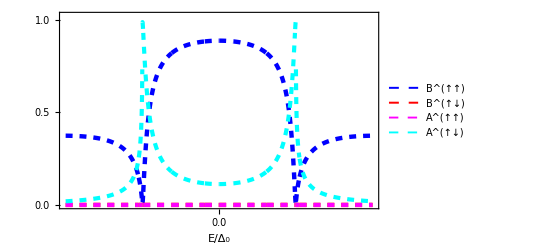

```mathematica
Plot[{Ruu1,Rud1,Rauu1,Raud1},{Ed,-2,2},PlotRange->{-0.0,1.02},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["B^(↑↑)",18,Black,Bold],Style["B^(↑↓)",18,Black,Bold],Style["A^(↑↑)",18,Black,Bold],Style["A^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

```mathematica
Ruu1n=(B11/.{m1-> -0.49999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Rud1n=(B12/.{m1-> -0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Rauu1n=(A11/.{m1->-0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Raud1n=(A12/.{m1->-0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Ruu1n/.{Ed-> 0.002}
```

0.00750791

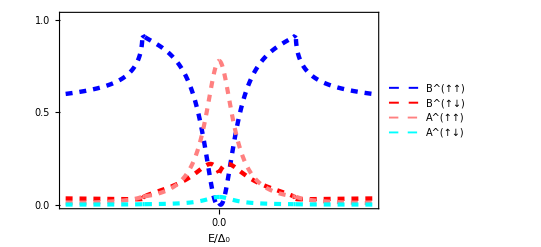

```mathematica
Plot[{Ruu1n,Rud1n,Rauu1n,Raud1n},{Ed,-2,2},PlotRange->{-0.0015,1.02},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Pink,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["B^(↑↑)",18,Black,Bold],Style["B^(↑↓)",18,Black,Bold],Style["A^(↑↑)",18,Black,Bold],Style["A^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{1,"1.0"},{15,"15.0"},{-1,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

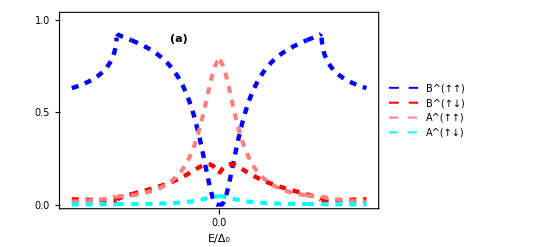

```mathematica
Ruu0n=(B11/.{m1-> -0.49999,Z-> 1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
Rud0n=(B12/.{m1-> -0.499999,Z->1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Rauu0n=(A11/.{m1->-0.499999,Z-> 1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
Raud0n=(A12/.{m1->-0.499999,Z-> 1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

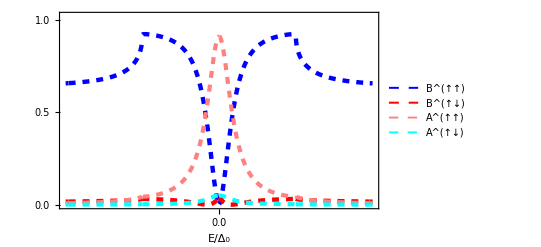

```mathematica
Plot[{Ruu0n,Rud0n,Rauu0n,Raud0n},{Ed,-2,2},PlotRange->{-0.0015,1.02},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Pink,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["B^(↑↑)",18,Black,Bold],Style["B^(↑↓)",18,Black,Bold],Style["A^(↑↑)",18,Black,Bold],Style["A^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{1,"1.0"},{15,"15.0"},{-1,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

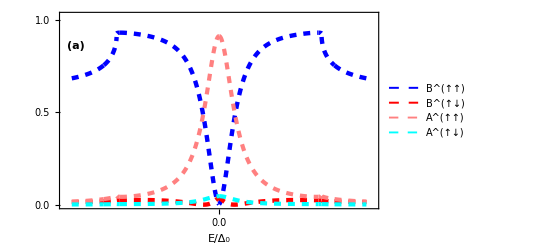

```mathematica
Tuu1=(Te11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> 0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Tud1=(Te12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> 0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Thuu1=(Th11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> 0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Thud1=(Th12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> 0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
(* 𝒯 = [ScriptCapitalT]*)
```

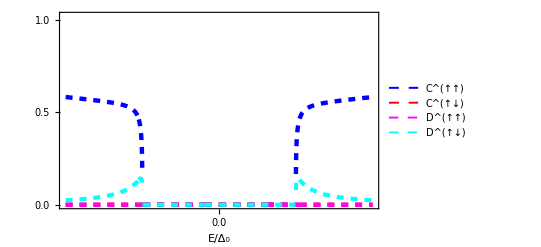

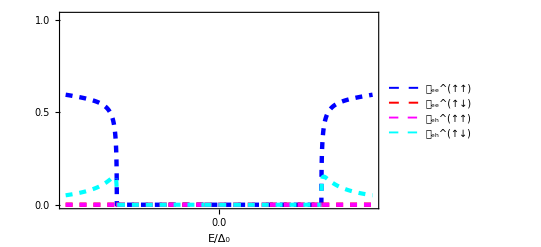

```mathematica
Plot[{Tuu1,Tud1,Thuu1,Thud1},{Ed,-2,2},PlotRange->{-0.001,1.02},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["C^(↑↑)",18,Black,Bold],Style["C^(↑↓)",18,Black,Bold],Style["D^(↑↑)",18,Black,Bold],Style["D^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{1,"1.0"},{15,"15.0"},{-1,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

```mathematica
Tuu1n=(Te11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Tud1n=(Te12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Thuu1n=(Th11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
Thud1n=(Th12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z-> 0.776,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
(* 𝒯 =\  [ScriptCapitalT]*)
```

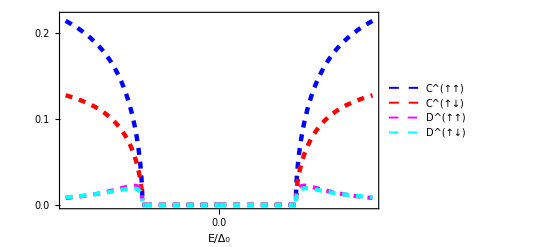

```mathematica
Plot[{Tuu1n,Tud1n,Thuu1n,Thud1n},{Ed,-2,2},PlotRange->{-0.0,0.22},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["C^(↑↑)",18,Black,Bold],Style["C^(↑↓)",18,Black,Bold],Style["D^(↑↑)",18,Black,Bold],Style["D^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.2,"0.2"},{0,"0.0"},{0.1,"0.1"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{1,"1.0"},{15,"15.0"},{-1,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

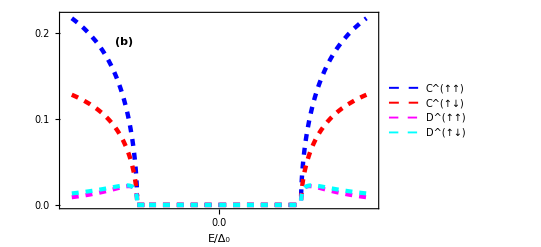

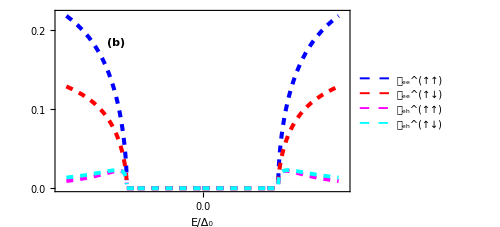

```mathematica
Tuu0n=(Te11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z->1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
Tud0n=(Te12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z->1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

```mathematica
Thuu0n=(Th11/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z->1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
Thud0n=(Th12/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),qp1-> qps,qm1-> qms}/.{m1-> -0.499999,Z-> 1.11,S->  0.5,kfa->  0.85*π,J-> 4.5});
```

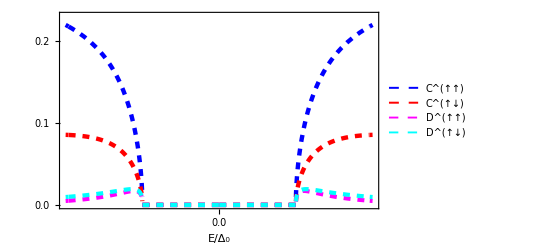

```mathematica
Plot[{Tuu0n,Tud0n,Thuu0n,Thud0n},{Ed,-2*Δ,2*Δ},PlotRange->{-0.0,0.23},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]},{Cyan,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["C^(↑↑)",18,Black,Bold],Style["C^(↑↓)",18,Black,Bold],Style["D^(↑↑)",18,Black,Bold],Style["D^(↑↓)",18,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{0.2,"0.2"},{0,"0.0"},{0.1,"0.1"}},None},{{{-5,"-5.0"},{5,"5.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}}, None}},FrameLabel-> {Style["E/Δ_0",22,Black,Bold,FontSlant->Italic],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

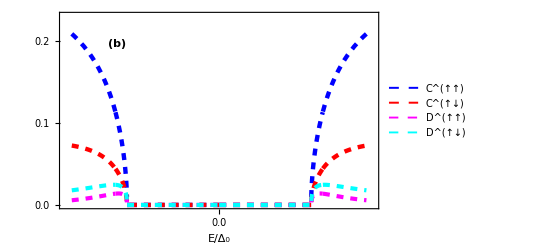

## Charge Δ_T noise NsfNIS

## Charge Thermovoltage

```mathematica
(*u=(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);v= (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);*)
ke1=(1+Abs[Ed]/(2*Ef));
kh1=(1-Abs[Ed]/(2*Ef));
qp1=(1+((Ed^2-Δ^2)^(1/2))/(2*Ef));
qm1=(1-((Ed^2-Δ^2)^(1/2))/(2*Ef));
```

```mathematica
(* Fermi function for numerical *)

f1e=1/(1+Exp[(Ed-V1)/kT1]); f2e=1/(1+Exp[(Ed-V2)/kT2]); 
f1h=1/(1+Exp[(Ed+V1)/kT1]);f2h=1/(1+Exp[(Ed+V2)/kT2]);
```

```mathematica
f1a=1/(1+Exp[(Ed-V)/kT]); f2a=1/(1+Exp[Ed/kT]);
DEf1a=D[f1a,Ed]; DEf2a=D[f2a,Ed];
DTf1a=D[f1a,kT]; DTf2a=D[f2a,kT];
```

```mathematica
f2e
```

1/(1+ⅇ^((Ed-V2)/kT2))

```mathematica
DEf1e=D[f1e,Ed]; DEf2e=D[f2e,Ed];  
DEf1h=D[f1h,Ed]; DEf2h=D[f2h,Ed]; 

DTf1e=D[f1e,kT1]; DTf2e=D[f2e,kT2]; 
DTf1h=D[f1h,kT1]; DTf2h=D[f2h,kT2];
```

```mathematica
f0=1/(1+Exp[Ed/kT]); fe=1/(1+Exp[(Ed-V)/kT]);  fh=1/(1+Exp[(Ed+V)/kT]);
DEfe=D[fe,Ed]; DTfe=D[fe,kT]; DEfh=D[fh,Ed]; DTfh=D[fh,kT];
DEf0=D[f0,Ed];DTf0=D[f0,kT];

DETfe=D[D[fe,kT],Ed]; DETfh=D[D[fh,kT],Ed];
 DETf0=D[D[f0,kT],Ed]; 
DT2fe=D[fe,{kT,2}]; DT2fh=D[fh,{kT,2}]; DT2f0=D[f0,{kT,2}];
DET2fe=D[D[fe,{kT,2}],Ed]; DET2fh=D[D[fh,{kT,2}],Ed];
 DET2f0=D[D[f0,{kT,2}],Ed];
```

```mathematica
kT1= k*T1;
kT2= k*T2; 
kT= k*T̄;
```

```mathematica
ΔT=T1-T2;  T̄=(T1+T2)/2;
```

```mathematica
k=8.617*10^-5;
 Δ=1; (* 0.00139;*)
S= 0.5;
Ef= 50*Δ;
kfa= 0.85*π;
J=4.5;
```

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
Δ=1;
```

```mathematica
(1-B11+A12)/.{m1->0.499999,Ed-> 1.5,Z-> 2.5,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5}
```

0.0931697

```mathematica
(1+A11-B11+A12-B12)/.{m1->0.499999,Ed->1.5,Z-> 2.5,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5}
```

0.0931694

```mathematica
Fth0=(1+A11-B11+A12-B12)+(1+A11d-B11d+A12d-B12d);
```

```mathematica
FI1=Fth0/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI2=Fth0/.{ m1-> -0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI3=Fth0/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI4=Fth0/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
FI1/.{Ed-> 0.001,Z-> 1}
```

-1.80638

```mathematica
Ichexpsf1[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI1*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf2[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI2*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf3[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI3*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf4[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI4*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
```

### spin configuration 1

```mathematica
f1a
```

1/(1+ⅇ^((23209.9 (Ed-V))/(T1+T2)))

```mathematica
DTf1a
```

(5.38701×10^8 ⅇ^((23209.9 (Ed-V))/(T1+T2)) (Ed-V))/((1+ⅇ^((23209.9 (Ed-V))/(T1+T2)))^2 (T1+T2)^2)

```mathematica
FI1*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,Ed-> 1,V-> 0.3,Z-> 1}
```

General::munfl: 0.0142857 5.45416274606×10^-1000 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Is1=(1+A11-B11+A12-B12)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1-> 0.499999,S->  0.5,Δ->1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is1,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.03,0.002},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.03}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
findVsp1[Z_?NumericQ]:=Module[{initialGuess,root},initialGuess=If[Z<1,0.1,0.1];(*Initial guess for FindRoot*)root=V/.First[FindRoot[NIntegrate[Ichexpsf1[V,Z,Ed],{Ed,-Infinity,Infinity}]==0,{V,initialGuess,0,1.5}]];
If[Abs[NIntegrate[Ichexpsf1[root,Z,Ed],{Ed,-Infinity,Infinity}]]>10^-8,Print["Warning: The root may not be accurate. Try refining the initial guess or changing the method."]];
root]

(*Create a table of results of thermovoltage for different Z values*)
Vthsp1=Table[{Z,findVsp1[Z]},{Z,0.001,2.1,0.2}];
```

NIntegrate::inumr: The integrand Ichexpsf1[V,0.001,Ed] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

```mathematica
findVsp10[Z_?NumericQ]:=V/.First[FindRoot[NIntegrate[Ichexpsf1[V,J0,Ec],{Ec,-Infinity,Infinity},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->10,WorkingPrecision->10]==0,{V,0.3}]]

(*Create a table of results of thermovoltage for different Z values*)
Vthsp10=Table[{J0,findVsp10[J0]},{J0,0.036,3.0,0.08}] ;
```

```mathematica
Vthsp1
```

```mathematica
Vthsp1={{0.036,0.000029952800000000002},{0.11599999999999999,0.0000299876},{0.196,0.000029983800000000003},{0.27599999999999997,0.000029897300000000003},{0.35600000000000004,0.0000300174},{0.43600000000000005,0.0000298397},{0.516,0.000029806300000000003},{0.596,0.0000298513},{0.676,0.0000294748},{0.756,0.0000298019},{0.836,0.0000297991},{0.916,0.0000339172},{0.9960000000000001,0.0000294689},{1.076,0.0000294689},{1.1560000000000001,0.0000294689},{1.236,0.000030565700000000005},{1.316,0.0000297971},{1.3960000000000001,0.0000297466},{1.476,0.0000307438},{1.556,0.0000415375},{1.6360000000000001,0.000039703299999999996},{1.7160000000000002,0.0000292455},{1.7960000000000003,0.0000307388},{1.8760000000000003,0.0000363195},{1.956,0.0000356475},{2.036,0.0000292919},{2.116,0.0000291424},{2.196,0.0000281244},{2.2760000000000002,0.0000297971},{2.356,0.0000436212},{2.436,0.0000366768},{2.516,0.0000319135},{2.596,0.000028767500000000002},{2.676,0.000036128300000000004},{2.7560000000000002,0.000036370100000000006},{2.8360000000000003,0.0000397761},{2.9160000000000004,0.0000389079},{2.9960000000000004,0.0000307388}}
```

{{0.036,0.0000299528},{0.116,0.0000299876},{0.196,0.0000299838},{0.276,0.0000298973},{0.356,0.0000300174},{0.436,0.0000298397},{0.516,0.0000298063},{0.596,0.0000298513},{0.676,0.0000294748},{0.756,0.0000298019},{0.836,0.0000297991},{0.916,0.0000339172},{0.996,0.0000294689},{1.076,0.0000294689},{1.156,0.0000294689},{1.236,0.0000305657},{1.316,0.0000297971},{1.396,0.0000297466},{1.476,0.0000307438},{1.556,0.0000415375},{1.636,0.0000397033},{1.716,0.0000292455},{1.796,0.0000307388},{1.876,0.0000363195},{1.956,0.0000356475},{2.036,0.0000292919},{2.116,0.0000291424},{2.196,0.0000281244},{2.276,0.0000297971},{2.356,0.0000436212},{2.436,0.0000366768},{2.516,0.0000319135},{2.596,0.0000287675},{2.676,0.0000361283},{2.756,0.0000363701},{2.836,0.0000397761},{2.916,0.0000389079},{2.996,0.0000307388}}

```mathematica
Remove[x0,listIsp1]
```

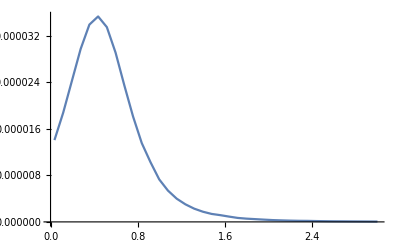

```mathematica
x0=1;listIsp1=ParallelTable[
Z=Vthsp1[[x0]][[1]];
V=Vthsp1[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp1=NIntegrate[Is1,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp1},
{x0,1,38,1}];
listIsp1=SortBy[listIsp1,First];
ListLinePlot[listIsp1,PlotRange->All]
```

```mathematica
Is2=(1+A11-B11+A12-B12)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1-> -0.499999,S->  0.5,Δ-> 1,Ef-> 50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is2,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.05,0.002},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.05}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp2
```

```mathematica
Vthsp2={{0.036,1.0605399999999999*^-6},{0.11599999999999999,1.8506100000000002*^-6},{0.196,2.5700100000000002*^-6},{0.27599999999999997,6.09689*^-6},{0.35600000000000004,2.08711*^-6},{0.43600000000000005,2.01766*^-6},{0.516,1.40185*^-6},{0.596,3.21486*^-6},{0.676,3.1806800000000006*^-6},{0.756,3.27792*^-6},{0.836,3.1463400000000005*^-6},{0.916,3.2143400000000006*^-6},{0.9960000000000001,3.38636*^-6},{1.076,4.12093*^-6},{1.1560000000000001,2.08711*^-6},{1.236,2.2845000000000003*^-6},{1.316,3.2141999999999997*^-6},{1.3960000000000001,2.66838*^-6},{1.476,3.49232*^-6},{1.556,3.8629700000000006*^-6},{1.6360000000000001,3.1463400000000005*^-6},{1.7160000000000002,1.4047100000000001*^-6},{1.7960000000000003,2.1847100000000003*^-6},{1.8760000000000003,3.66788*^-6},{1.956,3.8156500000000005*^-6},{2.036,3.97647*^-6},{2.116,4.15327*^-6},{2.196,2.3193400000000002*^-6},{2.2760000000000002,6.82539*^-7},{2.356,8.61888*^-6},{2.436,1.24532*^-6},{2.516,3.28276*^-6},{2.596,5.139090000000001*^-6},{2.676,3.38695*^-6},{2.7560000000000002,1.0514900000000002*^-6},{2.8360000000000003,5.6036200000000006*^-6},{2.9160000000000004,5.76014*^-6},{2.9960000000000004,5.95485*^-6}}
```

{{0.036,1.06054×10^-6},{0.116,1.85061×10^-6},{0.196,2.57001×10^-6},{0.276,6.09689×10^-6},{0.356,2.08711×10^-6},{0.436,2.01766×10^-6},{0.516,1.40185×10^-6},{0.596,3.21486×10^-6},{0.676,3.18068×10^-6},{0.756,3.27792×10^-6},{0.836,3.14634×10^-6},{0.916,3.21434×10^-6},{0.996,3.38636×10^-6},{1.076,4.12093×10^-6},{1.156,2.08711×10^-6},{1.236,2.2845×10^-6},{1.316,3.2142×10^-6},{1.396,2.66838×10^-6},{1.476,3.49232×10^-6},{1.556,3.86297×10^-6},{1.636,3.14634×10^-6},{1.716,1.40471×10^-6},{1.796,2.18471×10^-6},{1.876,3.66788×10^-6},{1.956,3.81565×10^-6},{2.036,3.97647×10^-6},{2.116,4.15327×10^-6},{2.196,2.31934×10^-6},{2.276,6.82539×10^-7},{2.356,8.61888×10^-6},{2.436,1.24532×10^-6},{2.516,3.28276×10^-6},{2.596,5.13909×10^-6},{2.676,3.38695×10^-6},{2.756,1.05149×10^-6},{2.836,5.60362×10^-6},{2.916,5.76014×10^-6},{2.996,5.95485×10^-6}}

```mathematica
Remove[x0,listIsp2]
```

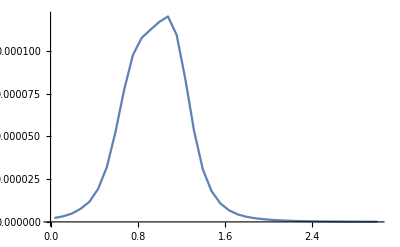

```mathematica
x0=1;listIsp2=ParallelTable[
Z=Vthsp2[[x0]][[1]];
V=Vthsp2[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp2=NIntegrate[Is2,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp2},
{x0,1,38,1}];
listIsp2=SortBy[listIsp2,First];
ListLinePlot[listIsp2,PlotRange->All]
```

```mathematica
listIsp2
```

{{0.036,2.279076649×10^-6},{0.116,3.283012539×10^-6},{0.196,4.875971756×10^-6},{0.276,7.670274336×10^-6},{0.356,0.00001177293116},{0.436,0.00001929483134},{0.516,0.00003201804258},{0.596,0.0000527970637},{0.676,0.00007762783312},{0.756,0.00009771770399},{0.836,0.0001076030358},{0.916,0.0001123165139},{0.996,0.0001168256876},{1.076,0.0001200550853},{1.156,0.0001092309359},{1.236,0.00008319862752},{1.316,0.00005292847197},{1.396,0.00003062522965},{1.476,0.00001792371294},{1.556,0.00001082252386},{1.636,6.762405972×10^-6},{1.716,4.366819376×10^-6},{1.796,2.987272607×10^-6},{1.876,2.122176043×10^-6},{1.956,1.533021555×10^-6},{2.036,1.134407539×10^-6},{2.116,8.572427376×10^-7},{2.196,6.489703427×10^-7},{2.276,4.999999241×10^-7},{2.356,4.224414197×10^-7},{2.436,3.193104657×10^-7},{2.516,2.635406532×10^-7},{2.596,2.193961175×10^-7},{2.676,1.790311358×10^-7},{2.756,1.466062848×10^-7},{2.836,1.280259835×10^-7},{2.916,1.086217611×10^-7},{2.996,9.279527712×10^-8}}

```mathematica
Is3=(1+A11d-B11d+A12d-B12d)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1->0.499999,S->  0.5,Δ->1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is3,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.08,0.005},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

$Aborted

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[listI,First].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of SortBy[listI,First].

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.8}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp3
```

```mathematica
Vthsp3={{0.04000000000000001,0.0000299603},{0.12,0.000029897300000000003},{0.2,0.0000298567},{0.27999999999999997,0.000029852900000000003},{0.36000000000000004,0.0000298476},{0.44000000000000006,0.0000305513},{0.52,0.000030076200000000002},{0.6000000000000001,0.0000292455},{0.68,0.000030127},{0.76,0.0000305624},{0.8400000000000001,0.0000297466},{0.9199999999999999,0.0000415209},{1.,0.0000341621},{1.08,0.000059476500000000006},{1.16,0.0000424825},{1.2400000000000002,0.0000292455},{1.32,0.0000433488},{1.4000000000000001,0.0000448046},{1.4800000000000002,0.0000294689},{1.56,0.0000314634},{1.64,0.0000307388},{1.72,0.000036301800000000005},{1.8,0.000038197},{1.8800000000000001,0.000040933900000000005},{1.9600000000000002,0.0000441093},{2.04,0.0000304605},{2.12,0.000030741},{2.2,0.0000361229},{2.2800000000000002,0.0000375786},{2.3600000000000003,0.0000374033},{2.44,0.0000361276},{2.52,0.0000349278},{2.6,0.0000294689},{2.68,0.0000531636},{2.7600000000000002,0.000028767500000000002},{2.84,0.00004093200000000001},{2.92,0.0000292919},{3.,0.0000413213}}
```

{{0.04,0.0000299603},{0.12,0.0000298973},{0.2,0.0000298567},{0.28,0.0000298529},{0.36,0.0000298476},{0.44,0.0000305513},{0.52,0.0000300762},{0.6,0.0000292455},{0.68,0.000030127},{0.76,0.0000305624},{0.84,0.0000297466},{0.92,0.0000415209},{1.,0.0000341621},{1.08,0.0000594765},{1.16,0.0000424825},{1.24,0.0000292455},{1.32,0.0000433488},{1.4,0.0000448046},{1.48,0.0000294689},{1.56,0.0000314634},{1.64,0.0000307388},{1.72,0.0000363018},{1.8,0.000038197},{1.88,0.0000409339},{1.96,0.0000441093},{2.04,0.0000304605},{2.12,0.000030741},{2.2,0.0000361229},{2.28,0.0000375786},{2.36,0.0000374033},{2.44,0.0000361276},{2.52,0.0000349278},{2.6,0.0000294689},{2.68,0.0000531636},{2.76,0.0000287675},{2.84,0.000040932},{2.92,0.0000292919},{3.,0.0000413213}}

```mathematica
Remove[x0,listIsp3]
```

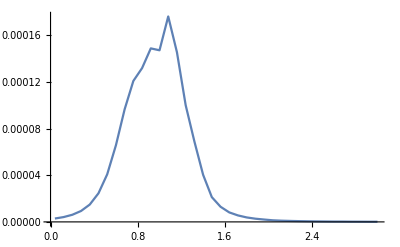

```mathematica
x0=1;listIsp3=ParallelTable[
Z=Vthsp3[[x0]][[1]];
V=Vthsp3[[x0]][[2]] ;
(*V=V1; Extract Vth for the current Z value*)
Ichsp3=NIntegrate[Is3,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp3},
{x0,1,38,1}];
listIsp3=SortBy[listIsp3,First];
ListLinePlot[listIsp3,PlotRange->All]
```

```mathematica
Is4=(1+A11d-B11d+A12d-B12d)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1->-0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is4,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.08,0.005},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.08}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp4
```

```mathematica
Vthsp4={{0.04000000000000001,0.0029952800000000003},{0.12,0.00299874},{0.2,0.00299838},{0.27999999999999997,0.0029897300000000003},{0.36000000000000004,0.00304166},{0.44000000000000006,0.0029839800000000002},{0.52,0.0029806200000000002},{0.6000000000000001,0.00297532},{0.68,0.00328727},{0.76,0.0029519200000000002},{0.8400000000000001,0.0030130400000000002},{0.9199999999999999,0.00294689},{1.,0.00294689},{1.08,0.00294689},{1.16,0.00292455},{1.2400000000000002,0.0030735800000000002},{1.32,0.00292455},{1.4000000000000001,0.0036415000000000006},{1.4800000000000002,0.0037048},{1.56,0.0030742100000000004},{1.64,0.00413245},{1.72,0.00292455},{1.8,0.0041324000000000005},{1.8800000000000001,0.00328276},{1.9600000000000002,0.0028124400000000003},{2.04,0.004132340000000001},{2.12,0.0037771000000000002},{2.2,0.00421493},{2.2800000000000002,0.0034519500000000005},{2.3600000000000003,0.0032483900000000003},{2.44,0.00345732},{2.52,0.00307388},{2.6,0.0033063299999999997},{2.68,0.0034519500000000005},{2.7600000000000002,0.006419460000000001},{2.84,0.0028124400000000003},{2.92,0.0029142400000000002},{3.,0.0034927800000000005}}
```

{{0.04,0.00299528},{0.12,0.00299874},{0.2,0.00299838},{0.28,0.00298973},{0.36,0.00304166},{0.44,0.00298398},{0.52,0.00298062},{0.6,0.00297532},{0.68,0.00328727},{0.76,0.00295192},{0.84,0.00301304},{0.92,0.00294689},{1.,0.00294689},{1.08,0.00294689},{1.16,0.00292455},{1.24,0.00307358},{1.32,0.00292455},{1.4,0.0036415},{1.48,0.0037048},{1.56,0.00307421},{1.64,0.00413245},{1.72,0.00292455},{1.8,0.0041324},{1.88,0.00328276},{1.96,0.00281244},{2.04,0.00413234},{2.12,0.0037771},{2.2,0.00421493},{2.28,0.00345195},{2.36,0.00324839},{2.44,0.00345732},{2.52,0.00307388},{2.6,0.00330633},{2.68,0.00345195},{2.76,0.00641946},{2.84,0.00281244},{2.92,0.00291424},{3.,0.00349278}}

```mathematica
Remove[x0,listIsp4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

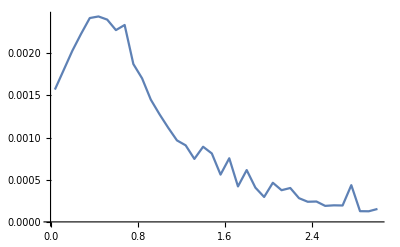

```mathematica
x0=1;listIsp4=ParallelTable[
Z=Vthsp4[[x0]][[1]];
V=Vthsp4[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp4=NIntegrate[Is4,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp4},
{x0,1,38,1}];
listIsp4=SortBy[listIsp4,First];
ListLinePlot[listIsp4,PlotRange->All]
```

## Charge Δ_T Thermal Noise

```mathematica
(* 2 factor multiplication to take the unit of 2e^2/h*)Fth1 =(1+A11-B11)/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5}; 

Fth21 =(1+A11-B11)/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fth22 =(A12-B12)/.{ m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fth31 =(1+A11d-B11d)/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fth32 =(A12d-B12d)/.{ m1-> 0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fth4 =(1+A11d-B11d)/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
Fermith1s=Simplify[- (k T1)DEfe- (k T2)DEf0+ (k*T̄) (- (k T1)DETfe+ (k T2)DETf0)(ΔT/(2 T̄))- (k*T̄)^2/2 ((k T1)DET2fe+(k T2)DET2f0)(ΔT/(2 T̄))^2,Element[Ed,Reals]]/.{V1-> V,V2->0};
Fermith1s=Simplify[-(k*T1*DEf1e+k*T2*DEf2e)]/.{V1-> V,V2->0}; (* f1e(1-f1e)+f2h(1-f2h)) *)
```

```mathematica
Sthc1=Fth1*Fermith1s/.{T1->4,T2->3};
Sthc21=Fth21*Fermith1s/.{T1->4,T2->3};
Sthc22=Fth22*Fermith1s/.{T1->4,T2->3};
Sthc31=Fth31*Fermith1s/.{T1->4,T2->3};
Sthc32=Fth32*Fermith1s/.{T1->4,T2->3};
Sthc4=Fth4*Fermith1s/.{T1->4,T2->3};
```

### Spin-configuration 1

```mathematica
Remove[x11,DTthsp1c];
```

```mathematica
x11 = 1;
listDTthsp1c=ParallelTable[
   Z=Vthsp1[[x11]][[1]];
   V=Vthsp1[[x11]][[2]]; (* 0.1 *)
Dthsp1=NIntegrate[Sthc1,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp1}, 
   {x11,1,38,1}];
DTthsp1c=SortBy[listDTthsp1c,First];(*Sort based on Z values*)
```

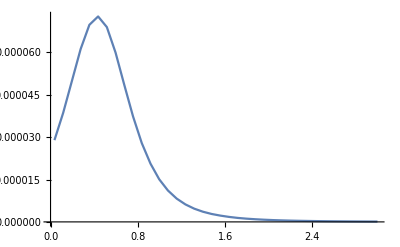

```mathematica
ListLinePlot[DTthsp1c,PlotRange->All]
```

### Spin-configuration 2

```mathematica
Vthsp2
```

{{0.036,1.06054×10^-6},{0.116,1.85061×10^-6},{0.196,2.57001×10^-6},{0.276,6.09689×10^-6},{0.356,2.08711×10^-6},{0.436,2.01766×10^-6},{0.516,1.40185×10^-6},{0.596,3.21486×10^-6},{0.676,3.18068×10^-6},{0.756,3.27792×10^-6},{0.836,3.14634×10^-6},{0.916,3.21434×10^-6},{0.996,3.38636×10^-6},{1.076,4.12093×10^-6},{1.156,2.08711×10^-6},{1.236,2.2845×10^-6},{1.316,3.2142×10^-6},{1.396,2.66838×10^-6},{1.476,3.49232×10^-6},{1.556,3.86297×10^-6},{1.636,3.14634×10^-6},{1.716,1.40471×10^-6},{1.796,2.18471×10^-6},{1.876,3.66788×10^-6},{1.956,3.81565×10^-6},{2.036,3.97647×10^-6},{2.116,4.15327×10^-6},{2.196,2.31934×10^-6},{2.276,6.82539×10^-7},{2.356,8.61888×10^-6},{2.436,1.24532×10^-6},{2.516,3.28276×10^-6},{2.596,5.13909×10^-6},{2.676,3.38695×10^-6},{2.756,1.05149×10^-6},{2.836,5.60362×10^-6},{2.916,5.76014×10^-6},{2.996,5.95485×10^-6}}

```mathematica
Remove[x11,DTthsp2c];
```

```mathematica
x11 = 1;
listDTthsp2c=ParallelTable[
   Z=Vthsp2[[x11]][[1]];
   V=Vthsp2[[x11]][[2]]; (* 0.1 *)
   Dthsp21=NIntegrate[Sthc21,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dthsp22=NIntegrate[Sthc22,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp21,Dthsp22}, 
   {x11,1,38,1}];
DTthsp2c=SortBy[listDTthsp2c,First];(*Sort based on Z values*)
```

```mathematica
DTthsp2c
```

{{0.036,0.0001052340726,-0.00009397961484},{0.116,0.00011661941,-0.0001005222239},{0.196,0.0001323886779,-0.0001086408352},{0.276,0.0001552710736,-0.0001189184395},{0.356,0.0001876904459,-0.0001303202335},{0.436,0.0002367713013,-0.0001428106559},{0.516,0.0003081118576,-0.0001514878436},{0.596,0.0004013462348,-0.0001459076716},{0.676,0.0004897474508,-0.0001119405448},{0.756,0.0005327294564,-0.00005430737715},{0.836,0.0005298640986,-4.055254014×10^-7},{0.916,0.0005212984166,0.00003158206713},{0.996,0.0005349535179,0.00003935939739},{1.076,0.0005674899485,0.00002064461879},{1.156,0.0005730886005,-0.00002642285373},{1.236,0.0005007708808,-0.00008124991673},{1.316,0.0003784374245,-0.0001118140479},{1.396,0.0002715451183,-0.000116430801},{1.476,0.000200075704,-0.0001099305307},{1.556,0.0001552453249,-0.0001010562773},{1.636,0.0001268199426,-0.00009284252876},{1.716,0.0001081672341,-0.00008597764167},{1.796,0.00009570498706,-0.00008063494839},{1.876,0.00008700391708,-0.00007642773812},{1.956,0.0000806158639,-0.00007299229319},{2.036,0.00007585402574,-0.00007022461696},{2.116,0.00007221996901,-0.00006797492362},{2.196,0.00006927379221,-0.00006601875861},{2.276,0.0000669326599,-0.00006439562266},{2.356,0.00006555052758,-0.00006352859859},{2.436,0.00006367407277,-0.00006206239929},{2.516,0.00006255796662,-0.00006124832017},{2.596,0.00006163107851,-0.00006055593628},{2.676,0.00006068141376,-0.00005979310777},{2.756,0.00005983465916,-0.00005909477791},{2.836,0.00005943346775,-0.00005880882873},{2.916,0.00005890104659,-0.00005837183147},{2.996,0.00005844225147,-0.00005799089858}}

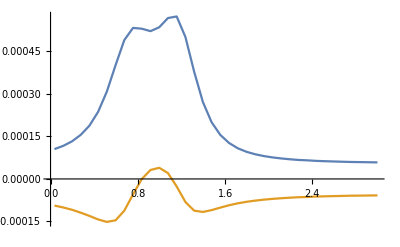

```mathematica
ListLinePlot[{DTthsp2c[[All,{1,2}]],DTthsp2c[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 3

```mathematica
Remove[x11,DTthsp3c];
```

```mathematica
x11 = 1;
listDTthsp3c=ParallelTable[
   Z=Vthsp3[[x11]][[1]];
   V=Vthsp3[[x11]][[2]]; (* 0.1 *)
   Dthsp31=NIntegrate[Sthc31,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dthsp32=NIntegrate[Sthc32,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp31,Dthsp32}, 
   {x11,1,38,1}];
DTthsp3c=SortBy[listDTthsp3c,First];(*Sort based on Z values*)
```

```mathematica
DTthsp3c
```

{{0.04,0.0001082491896,-0.00009652581515},{0.12,0.0001200051396,-0.0001032245772},{0.2,0.0001363322718,-0.0001115509433},{0.28,0.0001596992565,-0.0001218066076},{0.36,0.000194060313,-0.0001339519332},{0.44,0.0002454269553,-0.0001467786808},{0.52,0.0003197327373,-0.0001552607183},{0.6,0.0004149534426,-0.0001480755352},{0.68,0.0005042160725,-0.0001118831489},{0.76,0.0005454356315,-0.00005243987747},{0.84,0.0005408610922,1.807612588×10^-6},{0.92,0.0005378322164,0.00003357167873},{1.,0.0005499385763,0.0000400872512},{1.08,0.0005949227813,0.00001978912495},{1.16,0.0005906280069,-0.00003026158975},{1.24,0.0005062387322,-0.00008538002849},{1.32,0.0003846888482,-0.0001162763149},{1.4,0.0002764543819,-0.0001203106481},{1.48,0.0002015273854,-0.0001118490219},{1.56,0.0001570043346,-0.0001029133603},{1.64,0.0001285691839,-0.00009457976442},{1.72,0.0001105249897,-0.00008815180933},{1.8,0.00009802374908,-0.00008278949611},{1.88,0.0000892998455,-0.00007858214729},{1.96,0.00008301516332,-0.00007526094588},{2.04,0.00007730249742,-0.00007163334689},{2.12,0.00007364264583,-0.00006936311269},{2.2,0.00007108096806,-0.0000677774148},{2.28,0.00006887374824,-0.00006629043135},{2.36,0.00006701810288,-0.00006497164468},{2.44,0.00006544309163,-0.00006380259454},{2.52,0.00006413611521,-0.00006280585082},{2.6,0.0000628203548,-0.00006173421083},{2.68,0.0000631320108,-0.00006221573881},{2.76,0.00006117304755,-0.00006042284939},{2.84,0.00006113385483,-0.00006049644853},{2.92,0.00006001821105,-0.0000594830913},{3.,0.00006012243555,-0.00005966154367}}

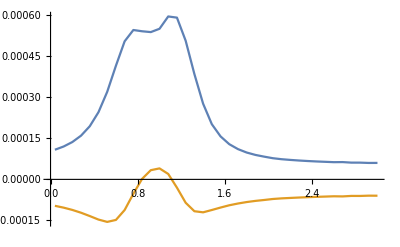

```mathematica
ListLinePlot[{DTthsp3c[[All,{1,2}]],DTthsp3c[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 4

```mathematica
Remove[x11,DTthsp4c];
```

```mathematica
x11 = 1;
listDTthsp4c=ParallelTable[
   Z=Vthsp4[[x11]][[1]];
   V=Vthsp4[[x11]][[2]]; (* 0.1 *)
   Dthsp4=NIntegrate[Sthc4,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp4}, 
   {x11,1,38,1}];
DTthsp4c=SortBy[listDTthsp4c,First];(*Sort based on Z values*)
```

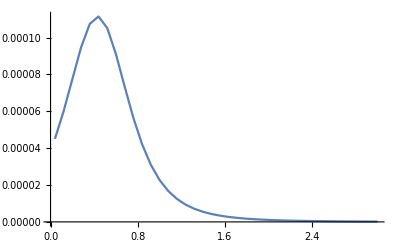

```mathematica
ListLinePlot[{DTthsp4c[[All,{1,2}]]},PlotRange->All]
```

```mathematica
DlTthc=ParallelTable[Flatten[{DTthsp1c[[pp]][[1]],(DTthsp1c[[pp]][[2]]+DTthsp4c[[pp]][[2]]+DTthsp2c[[pp]][[2]]+DTthsp3c[[pp]][[2]]),(DTthsp2c[[pp]][[3]]+DTthsp3c[[pp]][[3]]),DTthsp1c[[pp]][[2]]+DTthsp4c[[pp]][[2]]+DTthsp2c[[pp]][[2]]+DTthsp3c[[pp]][[2]]+(DTthsp2c[[pp]][[3]]+DTthsp3c[[pp]][[3]])}],{pp,1,38,1}]
```

{{0.036,0.0002874687436,-0.00019050543,0.0000969633136},{0.116,0.0003352914238,-0.0002037468011,0.000131544623},{0.196,0.0003960436494,-0.0002201917785,0.000175851871},{0.276,0.0004707960636,-0.0002407250471,0.000230071017},{0.356,0.0005589320791,-0.0002642721667,0.000294659912},{0.436,0.0006663906528,-0.0002895893367,0.000376801316},{0.516,0.0008020214544,-0.0003067485619,0.000495272892},{0.596,0.0009672438293,-0.0002939832068,0.000673260622},{0.676,0.001115911364,-0.0002238236937,0.000892087671},{0.756,0.001171976685,-0.0001067472546,0.00106522943},{0.836,0.001140783903,1.40208719×10^-6,0.00114218599},{0.916,0.00111078036,0.00006515374586,0.001175934106},{0.996,0.001122741793,0.00007944664859,0.001202188441},{1.076,0.001190295951,0.00004043374373,0.001230729695},{1.156,0.001184425244,-0.00005668444348,0.0011277408},{1.236,0.001022558169,-0.0001666299452,0.000855928223},{1.316,0.00077492914,-0.0002280903628,0.000546838777},{1.396,0.0005570699499,-0.0002367414491,0.000320328501},{1.476,0.0004086584326,-0.0002217795526,0.00018687888},{1.556,0.0003178177428,-0.0002039696376,0.000113848105},{1.636,0.0002598140636,-0.0001874222932,0.0000723917704},{1.716,0.0002222346174,-0.000174129451,0.0000481051664},{1.796,0.0001966035243,-0.0001634244445,0.00003317908},{1.876,0.0001786606317,-0.0001550098854,0.000023650746},{1.956,0.0001655755625,-0.0001482532391,0.000017322323},{2.036,0.0001547708979,-0.0001418579639,0.000012912934},{2.116,0.0001472152227,-0.0001373380363,9.8771864×10^-6},{2.196,0.0001414955003,-0.0001337961734,7.6993269×10^-6},{2.276,0.0001367754245,-0.000130686054,6.0893705×10^-6},{2.356,0.0001333999119,-0.0001285002433,4.8996686×10^-6},{2.436,0.0001298295649,-0.0001258649938,3.9645711×10^-6},{2.516,0.0001273081921,-0.000124054171,3.2540211×10^-6},{2.596,0.0001249837303,-0.0001222901471,2.6935832×10^-6},{2.676,0.0001242784919,-0.0001220088466,2.269645×10^-6},{2.756,0.000121414885,-0.0001195176273,1.897258×10^-6},{2.836,0.0001209255786,-0.0001193052773,1.620301×10^-6},{2.916,0.0001192353131,-0.0001178549228,1.38039×10^-6},{2.996,0.0001188438939,-0.0001176524423,1.191452×10^-6}}

```mathematica
\   [ScriptCapitalD]
```

```mathematica
𝒟
```

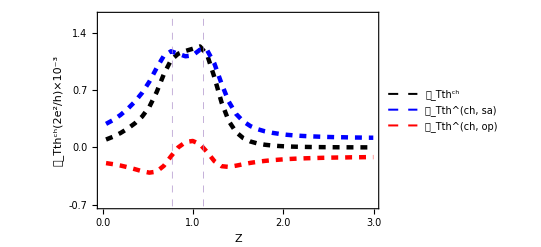

```mathematica
DSthc=ListLinePlot[{DlTthc[[All,{1,4}]],DlTthc[[All,{1,2}]],DlTthc[[All,{1,3}]]},PlotRange->{-0.0007,0.0016},GridLines-> {{0.77,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tth^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.0014,"1.4"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tth^ch",16,Bold],Style["𝒟_Tth^(ch, sa)",16,Bold],Style["𝒟_Tth^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

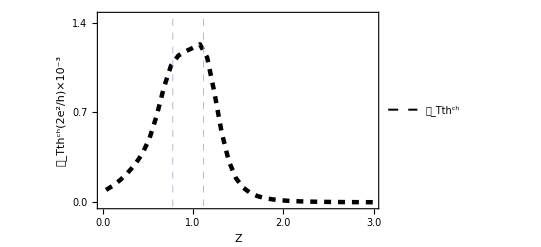

```mathematica
ListLinePlot[{DlTthc[[All,{1,4}]]},PlotRange->{-0.00002,0.00145},GridLines-> {{0.776,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tth^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.0014,"1.4"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tth^ch",16,Bold],Style["𝒟_Tth^(ch, sa)",16,Bold],Style["𝒟_Tth^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

## Charge Δ_T Shot Noise

```mathematica
Fsh1 =(A11(1-A11)+B11(1-B11)+2 A11*B11)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh21 =(A11(1-A11)+B11(1-B11)+2 A11*B11)/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fsh22 =A12*B12+A11*B12+A12*B11/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh31 =(A11d(1-A11d)+B11d(1-B11d)+2 A11d*B11d)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fsh32 =(A12d*B12d+A11d*B12d+A12d*B11d)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh4 =(A11d(1-A11d)+B11d(1-B11d)+2 A11d*B11d)/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
Fermish1s=Simplify[(fe-f0)^2+ 2 (k*T̄) (fe-fh) (DTfe+DTf0)(ΔT/(2 T̄)) + (k*T̄)^2 ( (DTfe-DTf0)^2+ (fe-fh) (DT2fe-DT2f0))(ΔT/(2 T̄))^2,Element[Ed,Reals]]/.{V1-> V,V2->0};
Fermish1s=Simplify[(f1e-f2e)^2]/.{V1-> V,V2->0}; (* f1e(1-f1e)+f2h(1-f2h)) *)
```

```mathematica
Sshc1=Fsh1*Fermish1s/.{T1->4,T2->3};
Sshc21=Fsh21*Fermish1s/.{T1->4,T2->3};
Sshc22=Fsh22*Fermish1s/.{T1->4,T2->3};
Sshc31=Fsh31*Fermish1s/.{T1->4,T2->3};
Sshc32=Fsh32*Fermish1s/.{T1->4,T2->3};
Sshc4=Fsh4*Fermish1s/.{T1->4,T2->3};
```

### Spin-configuration 1

```mathematica
Remove[x11,DTshsp1c];
```

```mathematica
x11 = 1;
listDTshsp1=ParallelTable[
   Z=Vthsp1[[x11]][[1]];
   V=Vthsp1[[x11]][[2]]; (* 0.1 *)
   Dshsp1=NIntegrate[Sshc1,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp1}, 
   {x11,1,38,1}];
DTshsp1c=SortBy[listDTshsp1,First](*Sort based on Z values*)
```

{{0.036,3.525178104×10^-7},{0.116,4.544178683×10^-7},{0.196,5.626263868×10^-7},{0.276,6.590537455×10^-7},{0.356,7.265280363×10^-7},{0.436,7.46185795×10^-7},{0.516,7.185239034×10^-7},{0.596,6.481368838×10^-7},{0.676,5.457157482×10^-7},{0.756,4.403064374×10^-7},{0.836,3.404436482×10^-7},{0.916,2.727049473×10^-7},{0.996,1.914784316×10^-7},{1.076,1.429384615×10^-7},{1.156,1.071485888×10^-7},{1.236,8.221759298×10^-8},{1.316,6.203133894×10^-8},{1.396,4.778712889×10^-8},{1.476,3.777634546×10^-8},{1.556,3.457251358×10^-8},{1.636,2.684210413×10^-8},{1.716,1.864424424×10^-8},{1.796,1.545621126×10^-8},{1.876,1.36860695×10^-8},{1.956,1.119337436×10^-8},{2.036,8.513948517×10^-9},{2.116,7.119440069×10^-9},{2.196,5.919604886×10^-9},{2.276,5.147835877×10^-9},{2.356,5.32479473×10^-9},{2.436,4.159685526×10^-9},{2.516,3.359671099×10^-9},{2.596,2.787196545×10^-9},{2.676,2.695081397×10^-9},{2.756,2.367154562×10^-9},{2.836,2.180570601×10^-9},{2.916,1.901320644×10^-9},{2.996,1.502273481×10^-9}}

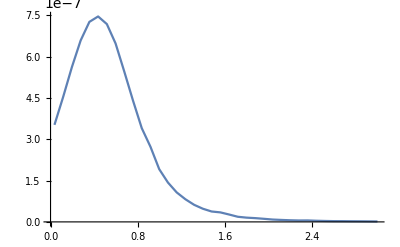

```mathematica
ListLinePlot[DTshsp1c,PlotRange->All]
```

### Spin-configuration 2

```mathematica
Remove[x11,DTshsp2c];
```

```mathematica
Remove[listDTshsp2]
```

```mathematica
x11 = 1;
listDTshsp2=ParallelTable[
   Z=Vthsp2[[x11]][[1]];
   V=Vthsp2[[x11]][[2]]; (* 0.1 *)
   Dshsp21=NIntegrate[Sshc21,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dshsp22=NIntegrate[Sshc22,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp21,Dshsp22}, 
   {x11,1,38,1}];
DTshsp2c=SortBy[listDTshsp2,First];(*Sort based on Z values*)
```

```mathematica
DTshsp2c
```

{{0.036,6.428356459×10^-7,3.826301435×10^-8},{0.116,6.966083024×10^-7,5.428282082×10^-8},{0.196,7.632198629×10^-7,7.891017399×10^-8},{0.276,8.841119235×10^-7,1.23254186×10^-7},{0.356,9.152290489×10^-7,1.760274662×10^-7},{0.436,9.95363685×10^-7,2.743350209×10^-7},{0.516,1.010766384×10^-6,4.241171318×10^-7},{0.596,9.188587567×10^-7,6.191275745×10^-7},{0.676,6.659475542×10^-7,6.475421331×10^-7},{0.756,5.37208204×10^-7,4.473852791×10^-7},{0.836,5.991974893×10^-7,2.710407794×10^-7},{0.916,6.439999061×10^-7,1.852037398×10^-7},{0.996,5.458979632×10^-7,1.139850427×10^-7},{1.076,3.247302136×10^-7,7.008372332×10^-8},{1.156,2.573346094×10^-7,2.330903063×10^-7},{1.236,6.769324466×10^-7,5.611225496×10^-7},{1.316,1.109504003×10^-6,5.802162112×10^-7},{1.396,1.157743798×10^-6,4.048689355×10^-7},{1.476,1.050749716×10^-6,2.655685191×10^-7},{1.556,9.140967636×10^-7,1.730278491×10^-7},{1.636,7.891077392×10^-7,1.131561143×10^-7},{1.716,6.84563064×10^-7,7.473113682×10^-8},{1.796,6.314371665×10^-7,5.274193527×10^-8},{1.876,5.998198284×10^-7,3.859025114×10^-8},{1.956,5.6621443×10^-7,2.828650307×10^-8},{2.036,5.40871359×10^-7,2.117038431×10^-8},{2.116,5.215289009×10^-7,1.61441803×10^-8},{2.196,4.906790144×10^-7,1.212609383×10^-8},{2.276,4.656404223×10^-7,9.271683597×10^-9},{2.356,5.159654841×10^-7,8.351542132×10^-9},{2.436,4.512358124×10^-7,5.987673994×10^-9},{2.516,4.588366024×10^-7,5.031519419×10^-9},{2.596,4.662339326×10^-7,4.25705145×10^-9},{2.676,4.484774273×10^-7,3.433923868×10^-9},{2.756,4.280323209×10^-7,2.766716783×10^-9},{2.836,4.560348769×10^-7,2.504028552×10^-9},{2.916,4.538252768×10^-7,2.129264279×10^-9},{2.996,4.523121162×10^-7,1.823347312×10^-9}}

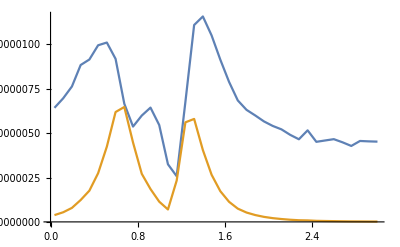

```mathematica
ListLinePlot[{DTshsp2c[[All,{1,2}]],DTshsp2c[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 3

```mathematica
Remove[x11,DTshsp3c];
```

```mathematica
x11 = 1;
listDTshsp3=ParallelTable[
   Z=Vthsp3[[x11]][[1]];
   V=Vthsp3[[x11]][[2]]; (* 0.1 *)
   Dshsp31=NIntegrate[Sshc31,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dshsp32=NIntegrate[Sshc32,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp31,Dshsp32}, 
   {x11,1,38,1}];
DTshsp3c=SortBy[listDTshsp3,First]
```

{{0.04,9.9747941×10^-7,3.657816882×10^-7},{0.12,1.067122182×10^-6,4.734951683×10^-7},{0.2,1.155972689×10^-6,5.925671033×10^-7},{0.28,1.26742581×10^-6,7.12347664×10^-7},{0.36,1.39727651×10^-6,8.295434894×10^-7},{0.44,1.534163587×10^-6,9.795000204×10^-7},{0.52,1.554627113×10^-6,1.19839433×10^-6},{0.6,1.343425056×10^-6,1.47600602×10^-6},{0.68,9.807333138×10^-7,1.504111048×10^-6},{0.76,8.094902298×10^-7,1.073743836×10^-6},{0.84,9.009728281×10^-7,6.74340173×10^-7},{0.92,1.129187427×10^-6,5.452383817×10^-7},{1.,8.491501657×10^-7,3.397985568×10^-7},{1.08,6.857877359×10^-7,3.513039818×10^-7},{1.16,4.837530341×10^-7,5.759276235×10^-7},{1.24,1.057452508×10^-6,8.988728092×10^-7},{1.32,2.017253822×10^-6,8.61554653×10^-7},{1.4,2.136509151×10^-6,4.421880213×10^-7},{1.48,1.542264217×10^-6,1.68220506×10^-7},{1.56,1.371982538×10^-6,8.938414282×10^-8},{1.64,1.186675925×10^-6,5.180089376×10^-8},{1.72,1.145453794×10^-6,3.648428096×10^-8},{1.8,1.072350687×10^-6,2.637559288×10^-8},{1.88,1.033904358×10^-6,2.035925913×10^-8},{1.96,1.017057466×10^-6,1.640988906×10^-8},{2.04,8.029198529×10^-7,1.078066012×10^-8},{2.12,7.75451598×10^-7,8.760777571×10^-9},{2.2,8.102191855×10^-7,7.767281629×10^-9},{2.28,8.053539896×10^-7,6.596416885×10^-9},{2.36,7.861107625×10^-7,5.533547447×10^-9},{2.44,7.583862379×10^-7,4.611742944×10^-9},{2.52,7.344282788×10^-7,3.876424157×10^-9},{2.6,6.71105188×10^-7,3.088006869×10^-9},{2.68,9.156352983×10^-7,3.688022002×10^-9},{2.76,6.507058489×10^-7,2.303079689×10^-9},{2.84,7.647609207×10^-7,2.387194695×10^-9},{2.92,6.454604986×10^-7,1.783079179×10^-9},{3.,7.584342468×10^-7,1.860319195×10^-9}}

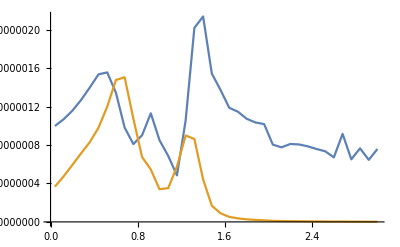

```mathematica
ListLinePlot[{DTshsp3c[[All,{1,2}]],DTshsp3c[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 4

```mathematica
Remove[x11,DTshsp4c];
```

```mathematica
x11 = 1;
listDTshsp4=ParallelTable[
   Z=Vthsp4[[x11]][[1]];
   V=Vthsp4[[x11]][[2]]0.01; (* 0.1 *)
   Dshsp4=NIntegrate[Sshc4,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp4}, 
   {x11,1,38,1}];
DTshsp4c=SortBy[listDTshsp4,First](*Sort based on Z values*)
```

{{0.04,3.572644066×10^-7},{0.12,4.597907847×10^-7},{0.2,5.679199227×10^-7},{0.28,6.632507665×10^-7},{0.36,7.328969216×10^-7},{0.44,7.459747787×10^-7},{0.52,7.159298047×10^-7},{0.6,6.427833334×10^-7},{0.68,5.670558316×10^-7},{0.76,4.332638127×10^-7},{0.84,3.374425606×10^-7},{0.92,2.524156814×10^-7},{1.,1.886960314×10^-7},{1.08,1.408742785×10^-7},{1.16,1.05298097×10^-7},{1.24,8.128863197×10^-8},{1.32,6.073367403×10^-8},{1.4,5.182332775×10^-8},{1.48,4.076736277×10^-8},{1.56,2.941500702×10^-8},{1.64,2.71377181×10^-8},{1.72,1.844658005×10^-8},{1.8,1.772295923×10^-8},{1.88,1.290725298×10^-8},{1.96,9.969974676×10^-9},{2.04,9.977827935×10^-9},{2.12,7.967435948×10^-9},{2.2,7.138692981×10^-9},{2.28,5.458883155×10^-9},{2.36,4.532356427×10^-9},{2.44,4.009626353×10^-9},{2.52,3.280447548×10^-9},{2.6,2.941860375×10^-9},{2.68,2.61759521×10^-9},{2.76,3.383493384×10^-9},{2.84,1.840302216×10^-9},{2.92,1.647997868×10^-9},{3.,1.584052312×10^-9}}

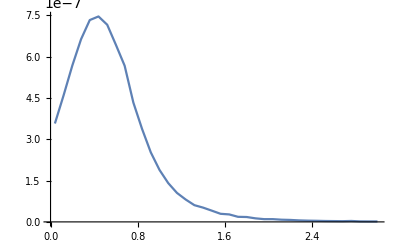

```mathematica
ListLinePlot[{DTshsp4c[[All,{1,2}]]},PlotRange->All]
```

```mathematica
DlTshc=ParallelTable[Flatten[{DTshsp1c[[pp]][[1]],DTshsp1c[[pp]][[2]]+DTshsp4c[[pp]][[2]]+DTshsp2c[[pp]][[2]]+DTshsp3c[[pp]][[2]],(DTshsp2c[[pp]][[3]]+DTshsp3c[[pp]][[3]]),DTshsp1c[[pp]][[2]]+DTshsp4c[[pp]][[2]]+DTshsp2c[[pp]][[2]]+DTshsp3c[[pp]][[2]]+(DTshsp2c[[pp]][[3]]+DTshsp3c[[pp]][[3]])}],{pp,1,38,1}]
```

{{0.036,2.702272815×10^-6,4.25006565×10^-7,3.12727938×10^-6},{0.116,3.04608997×10^-6,5.564655693×10^-7,3.602555539×10^-6},{0.196,3.43978445×10^-6,7.118046933×10^-7,4.151589143×10^-6},{0.276,3.85362212×10^-6,8.885491812×10^-7,4.742171301×10^-6},{0.356,4.250226053×10^-6,1.09757383×10^-6,5.347799883×10^-6},{0.436,4.543465233×10^-6,1.39768602×10^-6,5.941151253×10^-6},{0.516,4.544677326×10^-6,1.851259675×10^-6,6.395937×10^-6},{0.596,4.008400435×10^-6,2.402130542×10^-6,6.410530976×10^-6},{0.676,3.08999567×10^-6,2.473221015×10^-6,5.563216685×10^-6},{0.756,2.486091923×10^-6,1.74215304×10^-6,4.228244962×10^-6},{0.836,2.47652732×10^-6,1.080040815×10^-6,3.556568135×10^-6},{0.916,2.617864414×10^-6,8.221644484×10^-7,3.440028863×10^-6},{0.996,2.043664458×10^-6,5.098178296×10^-7,2.553482287×10^-6},{1.076,1.448206718×10^-6,4.547105419×10^-7,1.90291726×10^-6},{1.156,1.087869768×10^-6,9.30882278×10^-7,2.018752046×10^-6},{1.236,2.248742324×10^-6,1.750507823×10^-6,3.999250147×10^-6},{1.316,3.799884765×10^-6,1.729337327×10^-6,5.529222092×10^-6},{1.396,3.982157991×10^-6,1.052697963×10^-6,5.034855954×10^-6},{1.476,3.185638265×10^-6,5.636960852×10^-7,3.74933435×10^-6},{1.556,2.789328549×10^-6,3.455548041×10^-7,3.134883353×10^-6},{1.636,2.422217568×10^-6,2.212341313×10^-7,2.643451699×10^-6},{1.716,2.234857522×10^-6,1.513623301×10^-7,2.386219852×10^-6},{1.796,2.065474946×10^-6,1.065577008×10^-7,2.172032647×10^-6},{1.876,1.951273916×10^-6,7.766926783×10^-8,2.028943183×10^-6},{1.956,1.868923874×10^-6,5.790996148×10^-8,1.926833835×10^-6},{2.036,1.625660981×10^-6,4.226031583×10^-8,1.667921297×10^-6},{2.116,1.559155783×10^-6,3.255391827×10^-8,1.591709701×10^-6},{2.196,1.567651645×10^-6,2.616307867×10^-8,1.593814724×10^-6},{2.276,1.540924075×10^-6,2.103177969×10^-8,1.561955854×10^-6},{2.356,1.505183236×10^-6,1.70131405×10^-8,1.522196377×10^-6},{2.436,1.462842373×10^-6,1.385118411×10^-8,1.476693557×10^-6},{2.516,1.415592976×10^-6,1.127317915×10^-8,1.426866155×10^-6},{2.596,1.342522713×10^-6,9.166249336×10^-9,1.351688962×10^-6},{2.676,1.586139003×10^-6,8.781312427×10^-9,1.594920315×10^-6},{2.756,1.318134684×10^-6,6.580057229×10^-9,1.324714741×10^-6},{2.836,1.424558225×10^-6,5.987990937×10^-9,1.430546216×10^-6},{2.916,1.291938143×10^-6,4.799589364×10^-9,1.296737733×10^-6},{2.996,1.409266048×10^-6,4.471499425×10^-9,1.413737547×10^-6}}

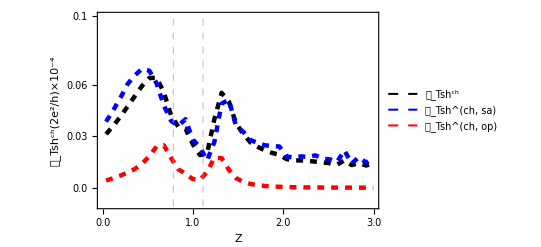

```mathematica
DSshc=ListLinePlot[{DlTshc[[All,{1,4}]],DlTsh[[All,{1,2}]],DlTshc[[All,{1,3}]]},PlotRange->{-0.000001,0.00001},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^ch(2e^2/h)×10^-4",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.000003,"0.03"},{0.00001,"0.1"},{0.000006,"0.06"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tsh^(ch, sa)",16,Bold],Style["𝒟_Tsh^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

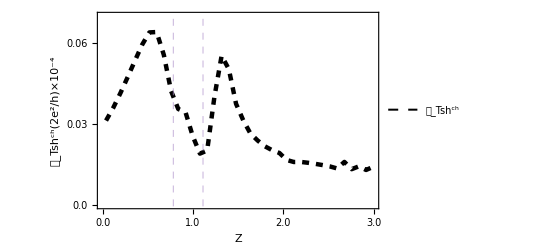

```mathematica
ListLinePlot[{DlTshc[[All,{1,4}]]},PlotRange->{-0.00,0.000007},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^ch(2e^2/h)×10^-4",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.000003,"0.03"},{0.00001,"0.1"},{0.000006,"0.06"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tsh^(ch, sa)",16,Bold],Style["𝒟_Tsh^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

```mathematica
DlTchc=ParallelTable[Flatten[{DlTthc[[pp]][[1]],DlTthc[[pp]][[2]]+DlTshc[[pp]][[2]],DlTthc[[pp]][[3]]+DlTshc[[pp]][[3]],DlTthc[[pp]][[4]]+DlTshc[[pp]][[4]],(DlTshc[[pp]][[4]]/(DlTthc[[pp]][[4]]))}],{pp,1,38,1}]
```

{{0.036,0.0002901710164,-0.000190080423,0.000100090593,0.0322521917},{0.116,0.0003383375138,-0.000203190336,0.000135147178,0.0273865664},{0.196,0.0003994834338,-0.000219479974,0.00018000346,0.0236084446},{0.276,0.0004746496857,-0.000239836498,0.000234813188,0.0206117718},{0.356,0.0005631823051,-0.000263174593,0.000300007712,0.0181490581},{0.436,0.000670934118,-0.000288191651,0.000382742467,0.0157673315},{0.516,0.0008065661317,-0.000304897302,0.000501668829,0.0129139654},{0.596,0.0009712522297,-0.000291581076,0.000679671153,0.00952161876},{0.676,0.00111900136,-0.000221350473,0.000897650887,0.00623617708},{0.756,0.001174462777,-0.000105005102,0.00106945767,0.00396932796},{0.836,0.001143260431,2.482128×10^-6,0.00114574256,0.00311382574},{0.916,0.001113398225,0.00006597591031,0.001179374135,0.00292535853},{0.996,0.001124785457,0.00007995646642,0.001204741924,0.00212402831},{1.076,0.001191744158,0.00004088845428,0.001232632612,0.00154616994},{1.156,0.001185513114,-0.0000557535612,0.00112975955,0.00179008514},{1.236,0.001024806911,-0.000164879437,0.000859927473,0.00467241299},{1.316,0.0007787290247,-0.000226361025,0.000552367999,0.0101112473},{1.396,0.0005610521079,-0.000235688751,0.000325363357,0.0157177895},{1.476,0.0004118440709,-0.000221215857,0.000190628214,0.0200629111},{1.556,0.0003206070714,-0.000203624083,0.000116982989,0.0275356656},{1.636,0.0002622362811,-0.000187201059,0.0000750352221,0.0365159145},{1.716,0.0002244694749,-0.000173978089,0.0000504913862,0.0496042324},{1.796,0.0001986689993,-0.000163317887,0.000035351112,0.065463921},{1.876,0.0001806119056,-0.000154932216,0.000025679689,0.085787703},{1.956,0.0001674444863,-0.000148195329,0.000019249157,0.11123415},{2.036,0.0001563965588,-0.000141815704,0.000014580855,0.12916672},{2.116,0.0001487743785,-0.000137305482,0.000011468896,0.16115011},{2.196,0.0001430631519,-0.00013377001,9.2931416×10^-6,0.20700702},{2.276,0.0001383163486,-0.000130665022,7.6513264×10^-6,0.25650531},{2.356,0.0001349050951,-0.00012848323,6.421865×10^-6,0.31067333},{2.436,0.0001312924073,-0.000125851143,5.4412646×10^-6,0.37247246},{2.516,0.0001287237851,-0.000124042898,4.6808873×10^-6,0.43849321},{2.596,0.000126326253,-0.000122280981,4.0452721×10^-6,0.50181816},{2.676,0.0001258646309,-0.000122000065,3.8645657×10^-6,0.7027179},{2.756,0.0001227330196,-0.000119511047,3.2219724×10^-6,0.6982261},{2.836,0.0001223501368,-0.000119299289,3.0508476×10^-6,0.882889},{2.916,0.0001205272512,-0.000117850123,2.6771281×10^-6,0.9393993},{2.996,0.0001202531599,-0.000117647971,2.6051892×10^-6,1.186567}}

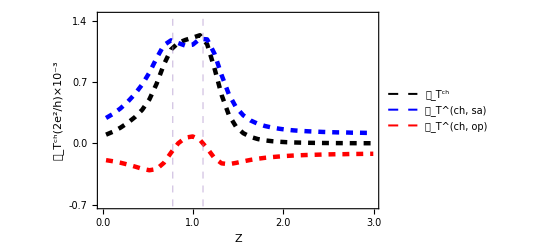

```mathematica
Dch=ListLinePlot[{DlTchc[[All,{1,4}]],DlTchc[[All,{1,2}]],DlTchc[[All,{1,3}]]},PlotRange->{-0.0007,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_T^(ch, sa)",16,Bold],Style["𝒟_T^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

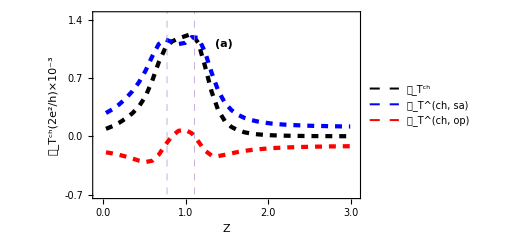

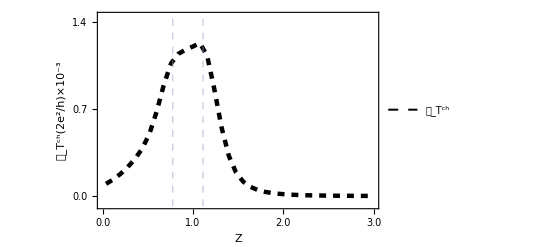

```mathematica
ListLinePlot[{DlTchc[[All,{1,4}]]},PlotRange->{-0.00007,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_T^(ch, sa)",16,Bold],Style["𝒟_T^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

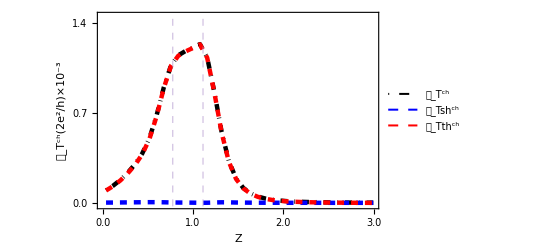

```mathematica
ListLinePlot[{DlTchc[[All,{1,4}]],DlTshc[[All,{1,4}]],DlTthc[[All,{1,4}]]},PlotRange->{-0.000015,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

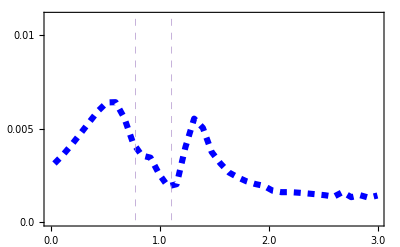

```mathematica
Dsh=ListLinePlot[{DlTshc[[All,{1,4}]]},PlotRange->{-0.00,0.000011},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Directive[Pink,Thickness[0.006]],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.011]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,13,Bold],FrameLabel-> {Style["",22,Black,Bold,FontSlant->Italic],Style["",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.00003,"0.03"},{0.00001,"0.01"},{0.000005,"0.005"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,15,Black}]
```

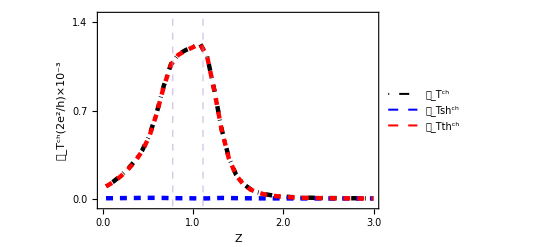

```mathematica
xyMinMax={{0.02,2.001},{-.00002,0.00005}};

ListLinePlot[{DlTchc[[All,{1,4}]],DlTshc[[All,{1,4}]],DlTthc[[All,{1,4}]]},PlotRange->{-0.00005,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large},Epilog->{Transparent,EdgeForm[{Pink,Thick}],Rectangle[Sequence@@Transpose[xyMinMax]],Inset[Dsh,Scaled[{.11,.65}],Scaled[{0,0}],2.07],PlotRange->{-0.2,0.003},PlotRangeClipping->False}]
```

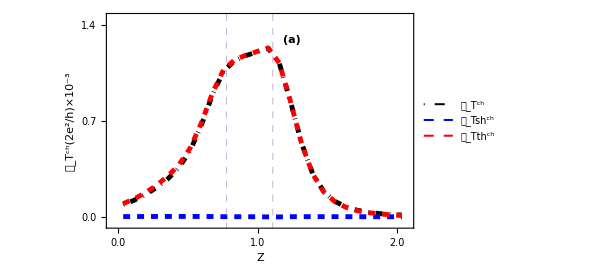

```mathematica
DlTchcs[[All,{1,5}]]
```

{{0.036,0.0322521917},{0.116,0.0273865664},{0.196,0.0236084446},{0.276,0.0206117718},{0.356,0.0181490581},{0.436,0.0157673315},{0.516,0.0129139654},{0.596,0.00952161876},{0.676,0.00623617708},{0.756,0.00396932796},{0.836,0.00311382574},{0.916,0.00292535853},{0.996,0.00212402831},{1.076,0.00154616994},{1.156,0.00179008514},{1.236,0.00467241299},{1.316,0.0101112473},{1.396,0.0157177895},{1.476,0.0200629111},{1.556,0.0275356656},{1.636,0.0365159145},{1.716,0.0496042324},{1.796,0.065463921},{1.876,0.085787703},{1.956,0.11123415},{2.036,0.12916672}}

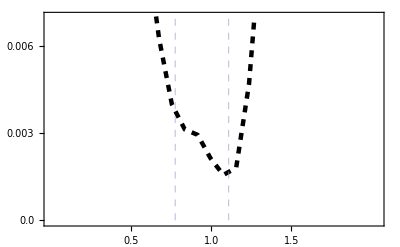

```mathematica
Pshth1=ListLinePlot[{DlTchcs[[All,{1,5}]]},PlotRange->{-0.00007,.007},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,14,Bold],FrameLabel-> {Style["",22,Black,Bold,FontSlant->Italic],Style["",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.006,"0.006"},{0.003,"0.003"},{2.14,"2.14"},{0.0,"0.0"}},None},{{{0.5,"0.5"},{1,"1.0"},{1.5,"1.5"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

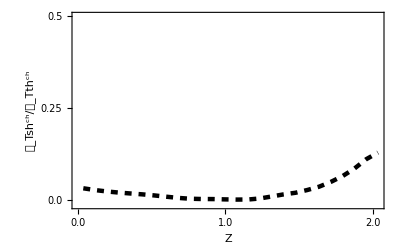

```mathematica
xyMinMax={{1.6,.4},{-.0123,.017}};

PDshth=ListLinePlot[{DlTchcs[[All,{1,5}]]},PlotRange->{-0.013,.5},Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^ch/𝒟_Tth^ch",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.5,"0.5"},{0.25,"0.25"},{2.14,"2.14"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large},Epilog->{Transparent,EdgeForm[{Red,Thick}],Rectangle[Sequence@@Transpose[xyMinMax]],Inset[Pshth1,Scaled[{.16,.52}],Scaled[{0,0}],1.68],PlotRange->{-0.2,0.003},PlotRangeClipping->False}]
```

## Spin Δ_T noise NsfNIS

## Spin Thermovoltage

```mathematica
(*u=(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);v= (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2);*)
ke1=(1+Abs[Ed]/(2*Ef));
kh1=(1-Abs[Ed]/(2*Ef));
qp1=(1+((Ed^2-Δ^2)^(1/2))/(2*Ef));
qm1=(1-((Ed^2-Δ^2)^(1/2))/(2*Ef));
```

```mathematica
(* Fermi function for numerical *)

f1e=1/(1+Exp[(Ed-V1)/kT1]); f2e=1/(1+Exp[(Ed-V2)/kT2]); 
f1h=1/(1+Exp[(Ed+V1)/kT1]);f2h=1/(1+Exp[(Ed+V2)/kT2]);
```

```mathematica
f1a=1/(1+Exp[(Ed-V)/kT]); f2a=1/(1+Exp[Ed/kT]);
DEf1a=D[f1a,Ed]; DEf2a=D[f2a,Ed];
DTf1a=D[f1a,kT]; DTf2a=D[f2a,kT];
```

```mathematica
f2e
```

1/(1+ⅇ^((Ed-V2)/kT2))

```mathematica
DEf1e=D[f1e,Ed]; DEf2e=D[f2e,Ed];  
DEf1h=D[f1h,Ed]; DEf2h=D[f2h,Ed]; 

DTf1e=D[f1e,kT1]; DTf2e=D[f2e,kT2]; 
DTf1h=D[f1h,kT1]; DTf2h=D[f2h,kT2];
```

```mathematica
f0=1/(1+Exp[Ed/kT]); fe=1/(1+Exp[(Ed-V)/kT]);  fh=1/(1+Exp[(Ed+V)/kT]);
DEfe=D[fe,Ed]; DTfe=D[fe,kT]; DEfh=D[fh,Ed]; DTfh=D[fh,kT];
DEf0=D[f0,Ed];DTf0=D[f0,kT];

DETfe=D[D[fe,kT],Ed]; DETfh=D[D[fh,kT],Ed];
 DETf0=D[D[f0,kT],Ed]; 
DT2fe=D[fe,{kT,2}]; DT2fh=D[fh,{kT,2}]; DT2f0=D[f0,{kT,2}];
DET2fe=D[D[fe,{kT,2}],Ed]; DET2fh=D[D[fh,{kT,2}],Ed];
 DET2f0=D[D[f0,{kT,2}],Ed];
```

```mathematica
kT1= k*T1;
kT2= k*T2; 
kT= k*T̄;
```

```mathematica
ΔT=T1-T2;  T̄=(T1+T2)/2;
```

```mathematica
k=8.617*10^-5;
 Δ=1; (* 0.00139;*)
S= 0.5;
Ef= 50*Δ;
kfa= 0.85*π;
J=4.5;
```

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
Fth0s=(1+A11-B11+A12-B12)-(1+A11d-B11d+A12d-B12d);
```

```mathematica
FI1s=1+A11-B11/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI2s=A12-B12/.{ m1-> -0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI3s=1+A11d-B11d/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
FI4s=A12d-B12d/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
FI1s/.{Ed-> 0.001,Z-> 1}
```

0.0480551

```mathematica
Ichexpsf1s[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI1s*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf2s[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI2s*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf3s[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI3s*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
Ichexpsf4s[V_?NumericQ,Z_?NumericQ,Ed_?NumericQ]:=FI4s*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3}
```

### spin configuration 1

```mathematica
f1a
```

1/(1+ⅇ^((23209.9 (Ed-V))/(T1+T2)))

```mathematica
DTf1a
```

(5.38701×10^8 ⅇ^((23209.9 (Ed-V))/(T1+T2)) (Ed-V))/((1+ⅇ^((23209.9 (Ed-V))/(T1+T2)))^2 (T1+T2)^2)

```mathematica
FI1*((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,Ed-> 1,V-> 0.3,Z-> 1}
```

General::munfl: 0.0142857 5.45416274606×10^-1000 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Is1s=(1+A11-B11)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1-> 0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is1s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.03,0.002},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.03}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
findVsp1[Z_?NumericQ]:=Module[{initialGuess,root},initialGuess=If[Z<1,0.1,0.1];(*Initial guess for FindRoot*)root=V/.First[FindRoot[NIntegrate[Ichexpsf1s[V,Z,Ed],{Ed,-Infinity,Infinity}]==0,{V,initialGuess,0,1.5}]];
If[Abs[NIntegrate[Ichexpsf1s[root,Z,Ed],{Ed,-Infinity,Infinity}]]>10^-8,Print["Warning: The root may not be accurate. Try refining the initial guess or changing the method."]];
root]

(*Create a table of results of thermovoltage for different Z values*)
Vthsp1s=Table[{Z,findVsp1[Z]},{Z,0.001,2.1,0.2}];
```

NIntegrate::inumr: The integrand Ichexpsf1[V,0.001,Ed] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

```mathematica
Vthsp1s
```

{{0.036,0.000149764},{0.116,0.000149938},{0.196,0.000149919},{0.276,0.000149487},{0.356,0.000150087},{0.436,0.000149199},{0.516,0.000149032},{0.596,0.000149257},{0.676,0.000147374},{0.756,0.00014901},{0.836,0.000148996},{0.916,0.000169586},{0.996,0.000147345},{1.076,0.000147345},{1.156,0.000147345},{1.236,0.000152829},{1.316,0.000148986},{1.396,0.000148733},{1.476,0.000153719},{1.556,0.000207688},{1.636,0.000198517},{1.716,0.000146228},{1.796,0.000153694},{1.876,0.000181597},{1.956,0.000178238},{2.036,0.00014646},{2.116,0.000145712},{2.196,0.000140622},{2.276,0.000148986},{2.356,0.000218106},{2.436,0.000183384},{2.516,0.000159568},{2.596,0.000143838},{2.676,0.000180642},{2.756,0.000181851},{2.836,0.000198881},{2.916,0.00019454},{2.996,0.000153694}}

```mathematica
Remove[x0,listIsp1]
```

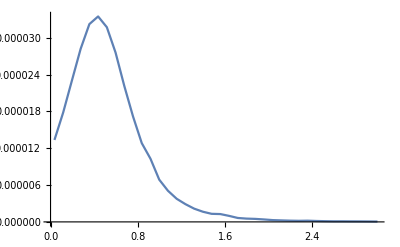

```mathematica
x0=1;listIsp1=ParallelTable[
Z=Vthsp1s[[x0]][[1]];
V=Vthsp1s[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp1=NIntegrate[Is1s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp1},
{x0,1,38,1}];
listIsp1=SortBy[listIsp1,First];
ListLinePlot[listIsp1,PlotRange->All]
```

```mathematica
Is2s=(A12-B12)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1-> -0.499999,S->  0.5,Δ-> 1,Ef-> 50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is2s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.05,0.002},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.05}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp2s
```

{{0.036,2.12108×10^-6},{0.116,3.70122×10^-6},{0.196,5.14002×10^-6},{0.276,0.0000121938},{0.356,4.17422×10^-6},{0.436,4.03532×10^-6},{0.516,2.8037×10^-6},{0.596,6.42972×10^-6},{0.676,6.36136×10^-6},{0.756,6.55584×10^-6},{0.836,6.29268×10^-6},{0.916,6.42868×10^-6},{0.996,6.77272×10^-6},{1.076,8.24186×10^-6},{1.156,4.17422×10^-6},{1.236,4.569×10^-6},{1.316,6.4284×10^-6},{1.396,5.33676×10^-6},{1.476,6.98464×10^-6},{1.556,7.72594×10^-6},{1.636,6.29268×10^-6},{1.716,2.80942×10^-6},{1.796,4.36942×10^-6},{1.876,7.33576×10^-6},{1.956,7.6313×10^-6},{2.036,7.95294×10^-6},{2.116,8.30654×10^-6},{2.196,4.63868×10^-6},{2.276,1.36508×10^-6},{2.356,0.0000172378},{2.436,2.49064×10^-6},{2.516,6.56552×10^-6},{2.596,0.0000102782},{2.676,6.7739×10^-6},{2.756,2.10298×10^-6},{2.836,0.0000112072},{2.916,0.0000115203},{2.996,0.0000119097}}

```mathematica
Remove[x0,listIsp2]
```

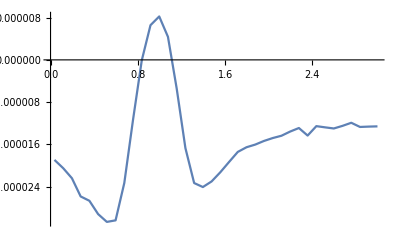

```mathematica
x0=1;listIsp2=ParallelTable[
Z=Vthsp2s[[x0]][[1]];
V=Vthsp2s[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp2=NIntegrate[Is2s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp2},
{x0,1,38,1}];
listIsp2=SortBy[listIsp2,First];
ListLinePlot[listIsp2,PlotRange->All]
```

```mathematica
Is3s=(A12d-B12d)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1->0.499999,S->  0.5,Δ->1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is3s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.08,0.005},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.8}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp3s
```

{{0.04,0.0000599206},{0.12,0.0000597946},{0.2,0.0000597134},{0.28,0.0000597058},{0.36,0.0000596952},{0.44,0.0000611026},{0.52,0.0000601524},{0.6,0.000058491},{0.68,0.000060254},{0.76,0.0000611248},{0.84,0.0000594932},{0.92,0.0000830418},{1.,0.0000683242},{1.08,0.000118953},{1.16,0.000084965},{1.24,0.000058491},{1.32,0.0000866976},{1.4,0.0000896092},{1.48,0.0000589378},{1.56,0.0000629268},{1.64,0.0000614776},{1.72,0.0000726036},{1.8,0.000076394},{1.88,0.0000818678},{1.96,0.0000882186},{2.04,0.000060921},{2.12,0.000061482},{2.2,0.0000722458},{2.28,0.0000751572},{2.36,0.0000748066},{2.44,0.0000722552},{2.52,0.0000698556},{2.6,0.0000589378},{2.68,0.000106327},{2.76,0.000057535},{2.84,0.000081864},{2.92,0.0000585838},{3.,0.0000826426}}

```mathematica
Remove[x0,listIsp3]
```

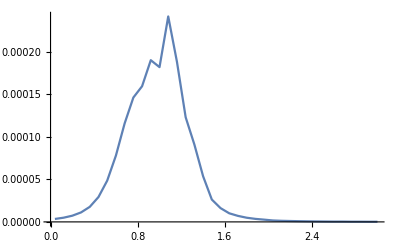

```mathematica
x0=1;listIsp3=ParallelTable[
Z=Vthsp3s[[x0]][[1]];
V=Vthsp3s[[x0]][[2]] ;
(*V=V1; Extract Vth for the current Z value*)
Ichsp3=NIntegrate[Is3,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp3},
{x0,1,38,1}];
listIsp3=SortBy[listIsp3,First];
ListLinePlot[listIsp3,PlotRange->All]
```

```mathematica
Is4s=(1+A11d-B11d)((f1a-f2a)+(DTf1a+DTf2a)*k*ΔT/2)/.{T1->4,T2->3,m1->-0.499999,S->  0.5,Δ-> 1,Ef->  50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
listI=ParallelTable[
ISz=Abs[ NIntegrate[Is4s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]]; (* INN= NIntegrate[FIN*DTfe*ΔT/.{T1->6,T2->4,Z-> 0.01},{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; *) 
{Z,V,ISz},(*Output Z,Intsh,Intth,Inttot,V*)
{V,0.0,0.08,0.005},{Z,0.01,2.1,0.2}];
listI=SortBy[listI,First];
```

```mathematica
listI=SortBy[Flatten[listI,1],First];

(*Extract Z,V,and INS values*)
{ZValues,VValues,INSValues}=Transpose[listI];

(*Reshape the INSValues array for plotting*)
n=Length[DeleteDuplicates[ZValues]];
m=Length[DeleteDuplicates[VValues]];
reshapedINSValues=Partition[INSValues,m];

(*Plotting the result*)
ListPlot3D[reshapedINSValues,DataRange->{{0,2},{0,0.08}},PlotRange->All,AxesLabel->{"Z","V","INS"}]
```

-Graphics3D-

```mathematica
Vthsp4s
```

{{0.04,0.0000299528},{0.12,0.0000299874},{0.2,0.0000299838},{0.28,0.0000298973},{0.36,0.0000304166},{0.44,0.0000298398},{0.52,0.0000298062},{0.6,0.0000297532},{0.68,0.0000328727},{0.76,0.0000295192},{0.84,0.0000301304},{0.92,0.0000294689},{1.,0.0000294689},{1.08,0.0000294689},{1.16,0.0000292455},{1.24,0.0000307358},{1.32,0.0000292455},{1.4,0.000036415},{1.48,0.000037048},{1.56,0.0000307421},{1.64,0.0000413245},{1.72,0.0000292455},{1.8,0.000041324},{1.88,0.0000328276},{1.96,0.0000281244},{2.04,0.0000413234},{2.12,0.000037771},{2.2,0.0000421493},{2.28,0.0000345195},{2.36,0.0000324839},{2.44,0.0000345732},{2.52,0.0000307388},{2.6,0.0000330633},{2.68,0.0000345195},{2.76,0.0000641946},{2.84,0.0000281244},{2.92,0.0000291424},{3.,0.0000349278}}

```mathematica
Remove[x0,listIsp4]
```

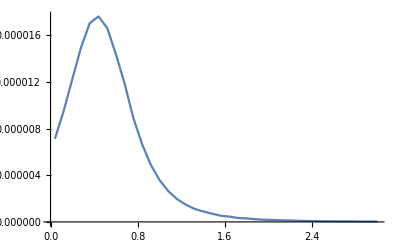

```mathematica
x0=1;listIsp4=ParallelTable[
Z=Vthsp4s[[x0]][[1]];
V=Vthsp4s[[x0]][[2]];
(*V=V1; Extract Vth for the current Z value*)
Ichsp4=NIntegrate[Is4s,{Ed,-∞,∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
{Z,Ichsp4},
{x0,1,38,1}];
listIsp4=SortBy[listIsp4,First];
ListLinePlot[listIsp4,PlotRange->All]
```

## Spin Δ_T Thermal Noise

```mathematica
(* 2 factor multiplication to take the unit of 2e^2/h*)Fth1 =(1+A11-B11)/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5}; 

Fth21 =(1+A11-B11)/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fth22 =(A12-B12)/.{ m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fth31 =(1+A11d-B11d)/.{ m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fth32 =(A12d-B12d)/.{ m1-> 0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fth4 =(1+A11d-B11d)/.{ m1-> -0.499999,S->  0.5,Δ->1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
Fermith1s=Simplify[- (k T1)DEfe- (k T2)DEf0+ (k*T̄) (- (k T1)DETfe+ (k T2)DETf0)(ΔT/(2 T̄))- (k*T̄)^2/2 ((k T1)DET2fe+(k T2)DET2f0)(ΔT/(2 T̄))^2,Element[Ed,Reals]]/.{V1-> V,V2->0};
Fermith1s=Simplify[-(k*T1*DEf1e+k*T2*DEf2e)]/.{V1-> V,V2->0}; (* f1e(1-f1e)+f2h(1-f2h)) *)
```

```mathematica
Sthc1s=Fth1*Fermith1s/.{T1->4,T2->3};
Sthc21s=Fth21*Fermith1s/.{T1->4,T2->3};
Sthc22s=Fth22*Fermith1s/.{T1->4,T2->3};
Sthc31s=Fth31*Fermith1s/.{T1->4,T2->3};
Sthc32s=Fth32*Fermith1s/.{T1->4,T2->3};
Sthc4s=Fth4*Fermith1s/.{T1->4,T2->3};
```

### Spin-configuration 1

```mathematica
Remove[x11,DTthsp1];
```

```mathematica
x11 = 1;
listDTthsp1=ParallelTable[
   Z=Vthsp1s[[x11]][[1]];
   V=Vthsp1s[[x11]][[2]]; 
Dthsp1=NIntegrate[Sthc1s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp1}, 
   {x11,1,38,1}];
DTthsp1=SortBy[listDTthsp1,First];(*Sort based on Z values*)
```

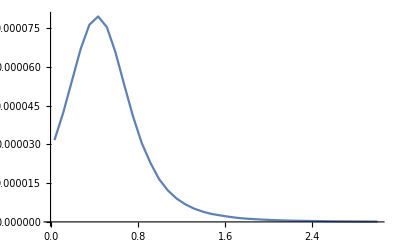

```mathematica
ListLinePlot[DTthsp1,PlotRange->All]
```

### Spin-configuration 2

```mathematica
Vthsp2s
```

{{0.036,1.06054×10^-6},{0.116,1.85061×10^-6},{0.196,2.57001×10^-6},{0.276,6.09689×10^-6},{0.356,2.08711×10^-6},{0.436,2.01766×10^-6},{0.516,1.40185×10^-6},{0.596,3.21486×10^-6},{0.676,3.18068×10^-6},{0.756,3.27792×10^-6},{0.836,3.14634×10^-6},{0.916,3.21434×10^-6},{0.996,3.38636×10^-6},{1.076,4.12093×10^-6},{1.156,2.08711×10^-6},{1.236,2.2845×10^-6},{1.316,3.2142×10^-6},{1.396,2.66838×10^-6},{1.476,3.49232×10^-6},{1.556,3.86297×10^-6},{1.636,3.14634×10^-6},{1.716,1.40471×10^-6},{1.796,2.18471×10^-6},{1.876,3.66788×10^-6},{1.956,3.81565×10^-6},{2.036,3.97647×10^-6},{2.116,4.15327×10^-6},{2.196,2.31934×10^-6},{2.276,6.82539×10^-7},{2.356,8.61888×10^-6},{2.436,1.24532×10^-6},{2.516,3.28276×10^-6},{2.596,5.13909×10^-6},{2.676,3.38695×10^-6},{2.756,1.05149×10^-6},{2.836,5.60362×10^-6},{2.916,5.76014×10^-6},{2.996,5.95485×10^-6}}

```mathematica
Remove[x11,DTthsp2];
```

```mathematica
x11 = 1;
listDTthsp2=ParallelTable[
   Z=Vthsp2s[[x11]][[1]];
   V=Vthsp2s[[x11]][[2]]; (* 0.1 *)
   Dthsp21=NIntegrate[Sthc21s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dthsp22=NIntegrate[Sthc22s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp21,Dthsp22}, 
   {x11,1,38,1}];
DTthsp2=SortBy[listDTthsp2,First];(*Sort based on Z values*)
```

```mathematica
DTthsp2
```

{{0.036,0.0001053264909,-0.00009406214804},{0.116,0.000116798001,-0.0001006761597},{0.196,0.000132670049,-0.0001088717243},{0.276,0.0001560515223,-0.0001195161236},{0.356,0.0001880145069,-0.0001305452139},{0.436,0.0002371665131,-0.0001430489845},{0.516,0.000308469371,-0.0001516635678},{0.596,0.0004024126534,-0.0001462952199},{0.676,0.0004910351654,-0.000112234825},{0.756,0.0005341731084,-0.00005445468278},{0.836,0.0005312425728,-4.067964546×10^-7},{0.916,0.0005226837676,0.00003166583975},{0.996,0.0005364508758,0.00003946954501},{1.076,0.0005694215681,0.0000207150101},{1.156,0.0005740783002,-0.00002646845069},{1.236,0.0005017174614,-0.00008140358177},{1.316,0.0003794432335,-0.0001121114042},{1.396,0.0002721445921,-0.0001166879466},{1.476,0.0002006533786,-0.0001102480141},{1.556,0.0001557409614,-0.0001013789601},{1.636,0.0001271499072,-0.00009308411206},{1.716,0.0001082930635,-0.00008607766374},{1.796,0.00009587801955,-0.00008078073953},{1.876,0.0000872676658,-0.00007665943055},{1.956,0.00008087005477,-0.00007322244925},{2.036,0.00007610324325,-0.00007045534119},{2.116,0.00007246775477,-0.00006820814609},{2.196,0.00006940672742,-0.00006614544798},{2.276,0.00006697050994,-0.00006443203812},{2.356,0.00006601538711,-0.0000639791203},{2.436,0.00006373973757,-0.00006212640213},{2.516,0.00006272773494,-0.00006141453458},{2.596,0.00006189248689,-0.00006081278465},{2.676,0.00006085129924,-0.00005996050642},{2.756,0.00005988676774,-0.00005914624217},{2.836,0.00005970822623,-0.00005908069963},{2.916,0.00005918091011,-0.00005864918055},{2.996,0.00005872927157,-0.00005827570208}}

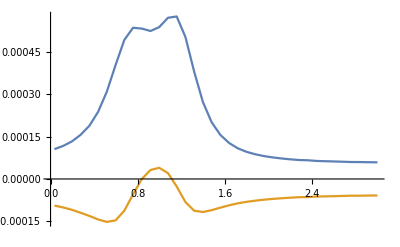

```mathematica
ListLinePlot[{DTthsp2[[All,{1,2}]],DTthsp2[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 3

```mathematica
Remove[x11,DTthsp3];
```

```mathematica
x11 = 1;
listDTthsp3=ParallelTable[
   Z=Vthsp3s[[x11]][[1]];
   V=Vthsp3s[[x11]][[2]]; (* 0.1 *)
   Dthsp31=NIntegrate[Sthc31s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dthsp32=NIntegrate[Sthc32s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp31,Dthsp32}, 
   {x11,1,38,1}];
DTthsp3=SortBy[listDTthsp3,First];(*Sort based on Z values*)
```

```mathematica
DTthsp3
```

{{0.04,0.0001108605163,-0.00009885429206},{0.12,0.0001228940799,-0.0001057094763},{0.2,0.0001396098279,-0.0001142325996},{0.28,0.0001635379378,-0.000124734222},{0.36,0.0001987239239,-0.0001371705837},{0.44,0.0002514591763,-0.0001503854436},{0.52,0.0003274732307,-0.000159018147},{0.6,0.0004247315537,-0.0001515633752},{0.68,0.0005164460942,-0.0001145964835},{0.76,0.0005588524882,-0.00005373135781},{0.84,0.0005538225983,1.8486163×10^-6},{0.92,0.0005555795372,0.00003467714181},{1.,0.0005649967533,0.00004118474582},{1.08,0.0006223967449,0.00002070531881},{1.16,0.0006105424048,-0.0000312812049},{1.24,0.000518172199,-0.00008739394834},{1.32,0.0003979149019,-0.0001202769019},{1.4,0.0002862616642,-0.0001245808557},{1.48,0.0002063142162,-0.000114506514},{1.56,0.0001609771305,-0.0001055179057},{1.64,0.0001317499571,-0.00009691988784},{1.72,0.0001137338062,-0.00009071123949},{1.8,0.0001010114754,-0.00008531298781},{1.88,0.00009220714563,-0.0000811405797},{1.96,0.00008591624077,-0.00007789108471},{2.04,0.00007919790744,-0.00007338977045},{2.12,0.00007546434857,-0.00007107896393},{2.2,0.00007313456315,-0.00006973557645},{2.28,0.0000709402367,-0.00006827941659},{2.36,0.0000690199234,-0.0000669123424},{2.44,0.00006733397968,-0.00006564608583},{2.52,0.00006593015953,-0.00006456268655},{2.6,0.00006431204261,-0.00006320010915},{2.68,0.00006576048922,-0.00006480607056},{2.76,0.00006259212067,-0.00006182452038},{2.84,0.00006312379051,-0.00006246563717},{2.92,0.00006143505284,-0.00006088730103},{3.,0.00006209712616,-0.00006162109703}}

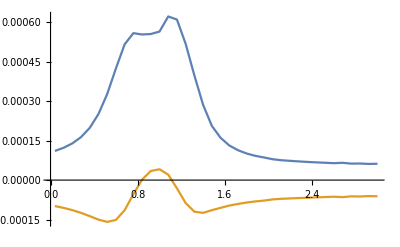

```mathematica
ListLinePlot[{DTthsp3[[All,{1,2}]],DTthsp3[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 4

```mathematica
Remove[x11,DTthsp4];
```

```mathematica
x11 = 1;
listDTthsp4=ParallelTable[
   Z=Vthsp4s[[x11]][[1]];
   V=Vthsp4s[[x11]][[2]]; 
   Dthsp4=NIntegrate[Sthc4s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dthsp4}, 
   {x11,1,38,1}];
DTthsp4=SortBy[listDTthsp4,First];(*Sort based on Z values*)
```

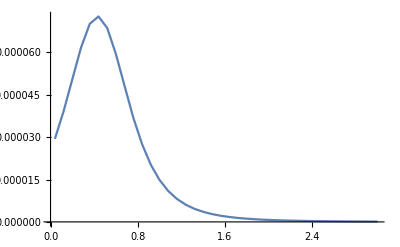

```mathematica
ListLinePlot[{DTthsp4[[All,{1,2}]]},PlotRange->All]
```

```mathematica
DlTth=ParallelTable[Flatten[{DTthsp1[[pp]][[1]],(DTthsp1[[pp]][[2]]+DTthsp4[[pp]][[2]]+DTthsp2[[pp]][[2]]+DTthsp3[[pp]][[2]]),(DTthsp2[[pp]][[3]]+DTthsp3[[pp]][[3]]),DTthsp1[[pp]][[2]]+DTthsp4[[pp]][[2]]+DTthsp2[[pp]][[2]]+DTthsp3[[pp]][[2]]-(DTthsp2[[pp]][[3]]+DTthsp3[[pp]][[3]])}],{pp,1,38,1}]
```

{{0.036,0.0002772591085,-0.0001929164401,0.0004701755486},{0.116,0.0003211554767,-0.000206385636,0.0005275411127},{0.196,0.0003774304005,-0.0002231043239,0.0006005347244},{0.276,0.0004483107177,-0.0002442503456,0.0006925610633},{0.356,0.000533232748,-0.0002677157977,0.0008009485456},{0.436,0.0006409352979,-0.0002934344281,0.000934369726},{0.516,0.0007800469838,-0.0003106817148,0.001090728699},{0.596,0.0009520971868,-0.0002978585951,0.001249955782},{0.676,0.00110852702,-0.0002268313085,0.001335358328},{0.756,0.001170720375,-0.0001081860406,0.001278906415},{0.836,0.001143108202,1.44181985×10^-6,0.00114166638},{0.916,0.001121314747,0.00006634298156,0.00105497176},{0.996,0.00113278386,0.00008065429083,0.00105212957},{1.076,0.001214902238,0.00004142032891,0.00117348191},{1.156,0.001201762528,-0.00005774965559,0.001259512184},{1.236,0.001032787825,-0.0001687975301,0.001201585355},{1.316,0.0007871315836,-0.0002323883061,0.00101951989},{1.396,0.0005659359513,-0.0002412688023,0.0008072047535},{1.476,0.0004128343605,-0.000224754528,0.0006375888886},{1.556,0.0003214109126,-0.0002068968658,0.0005283077783},{1.636,0.0002626337897,-0.0001900039999,0.0004526377896},{1.716,0.0002249566537,-0.0001767889032,0.0004017455569},{1.796,0.0001992832169,-0.0001660937273,0.0003653769442},{1.876,0.0001814472767,-0.0001578000103,0.000339247287},{1.956,0.0001684092383,-0.000151113534,0.0003195227722},{2.036,0.0001566422145,-0.0001438451116,0.0003004873262},{2.116,0.0001490538934,-0.00013928711,0.0002883410034},{2.196,0.0001434874288,-0.0001358810244,0.0002793684532},{2.276,0.0001387141538,-0.0001327114547,0.0002714256085},{2.356,0.0001357380374,-0.0001308914627,0.0002666295001},{2.436,0.0001316704408,-0.000127772488,0.0002594429288},{2.516,0.0001291679186,-0.0001259772211,0.0002551451397},{2.596,0.0001266448592,-0.0001240128938,0.000250657753},{2.676,0.0001270009828,-0.000124766577,0.0002517675597},{2.756,0.0001228235578,-0.0001209707625,0.0002437943204},{2.836,0.0001231327044,-0.0001215463368,0.0002446790412},{2.916,0.0001208809868,-0.0001195364816,0.0002404174683},{2.996,0.0001210581942,-0.0001198967991,0.0002409549933}}

```mathematica
\   [ScriptCapitalD]
```

```mathematica
𝒟
```

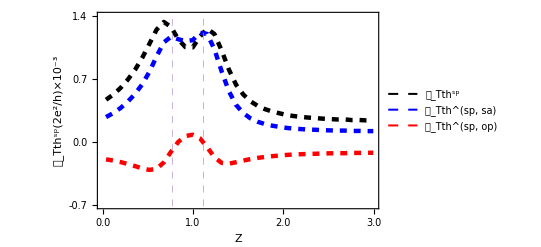

```mathematica
DSth=ListLinePlot[{DlTth[[All,{1,4}]],DlTth[[All,{1,2}]],DlTth[[All,{1,3}]]},PlotRange->{-0.0007,0.0014},GridLines-> {{0.77,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tth^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.0014,"1.4"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tth^sp",16,Bold],Style["𝒟_Tth^(sp, sa)",16,Bold],Style["𝒟_Tth^(sp, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

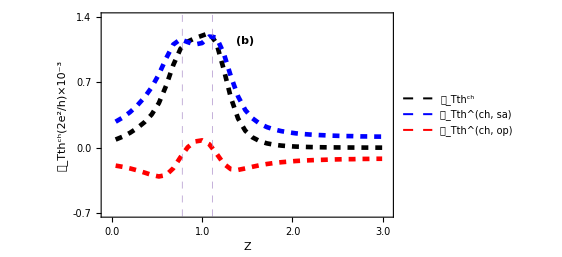

```mathematica
DlTth0
```

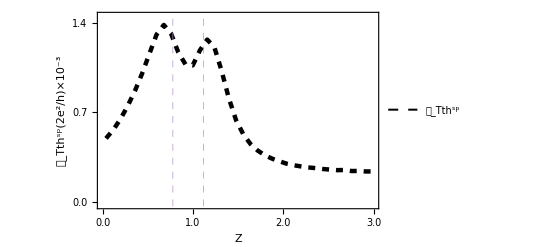

```mathematica
ListLinePlot[{DlTth[[All,{1,4}]]},PlotRange->{-0.00002,0.00145},GridLines-> {{0.776,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tth^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.0014,"1.4"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tth^sp",16,Bold],Style["𝒟_Tth^(ch, sa)",16,Bold],Style["𝒟_Tth^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

## Spin Δ_T Shot Noise

```mathematica
Fsh1 =(A11(1-A11)+B11(1-B11)+2 A11*B11)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh21 =(A11(1-A11)+B11(1-B11)+2 A11*B11)/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fsh22 =A12*B12+A11*B12+A12*B11/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh31 =(A11d(1-A11d)+B11d(1-B11d)+2 A11d*B11d)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
Fsh32 =(A12d*B12d+A11d*B12d+A12d*B11d)/.{m1-> 0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};

Fsh4 =(A11d(1-A11d)+B11d(1-B11d)+2 A11d*B11d)/.{m1-> -0.499999,S->  0.5,Δ-> 1,Ef->50*Δ,kfa->  0.85*π,J-> 4.5};
```

```mathematica
Fermish1s=Simplify[(fe-f0)^2+ 2 (k*T̄) (fe-fh) (DTfe+DTf0)(ΔT/(2 T̄)) + (k*T̄)^2 ( (DTfe-DTf0)^2+ (fe-fh) (DT2fe-DT2f0))(ΔT/(2 T̄))^2,Element[Ed,Reals]];
Fermish1s=Simplify[(f1e-f2e)^2]/.{V1-> V,V2->0}; (* f1e(1-f1e)+f2h(1-f2h)) *)
```

```mathematica
Sshc1s=Fsh1*Fermish1s/.{T1->4,T2->3};
Sshc21s=Fsh21*Fermish1s/.{T1->4,T2->3};
Sshc22s=Fsh22*Fermish1s/.{T1->4,T2->3};
Sshc31s=Fsh31*Fermish1s/.{T1->4,T2->3};
Sshc32s=Fsh32*Fermish1s/.{T1->4,T2->3};
Sshc4s=Fsh4*Fermish1s/.{T1->4,T2->3};
```

### Spin-configuration 1

```mathematica
Remove[x11,DTshsp1];
```

```mathematica
x11 = 1;
listDTshsp1=ParallelTable[
   Z=Vthsp1s[[x11]][[1]];
   V=Vthsp1s[[x11]][[2]]; (* 0.1 *)
   Dshsp1=NIntegrate[Sshc1s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp1}, 
   {x11,1,38,1}];
DTshsp1=SortBy[listDTshsp1,First](*Sort based on Z values*)
```

{{0.036,1.353058945×10^-6},{0.116,1.745995936×10^-6},{0.196,2.161516575×10^-6},{0.276,2.525425677×10^-6},{0.356,2.79400467×10^-6},{0.436,2.854371724×10^-6},{0.516,2.745802474×10^-6},{0.596,2.480170011×10^-6},{0.676,2.064684936×10^-6},{0.756,1.682386228×10^-6},{0.836,1.300706698×10^-6},{0.916,1.17239198×10^-6},{0.996,7.243185271×10^-7},{1.076,5.4070307×10^-7},{1.156,4.053182768×10^-7},{1.236,3.213739127×10^-7},{1.316,2.369840967×10^-7},{1.396,1.822887051×10^-7},{1.476,1.484373897×10^-7},{1.556,1.800534997×10^-7},{1.636,1.33865847×10^-7},{1.716,7.005025199×10^-8},{1.796,6.072431163×10^-8},{1.876,6.272222278×10^-8},{1.956,5.040643146×10^-8},{2.036,3.203382848×10^-8},{2.116,2.666529989×10^-8},{2.196,2.148534369×10^-8},{2.276,1.966675627×10^-8},{2.356,2.90732619×10^-8},{2.436,1.924012846×10^-8},{2.516,1.365674023×10^-8},{2.596,1.031998885×10^-8},{2.676,1.22901901×10^-8},{2.756,1.086271451×10^-8},{2.836,1.08939212×10^-8},{2.916,9.300757785×10^-9},{2.996,5.902126999×10^-9}}

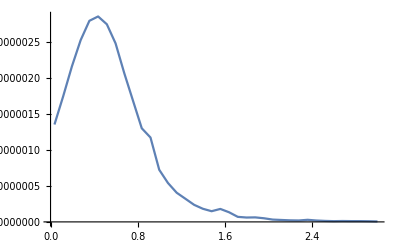

```mathematica
ListLinePlot[DTshsp1,PlotRange->All]
```

### Spin-configuration 2

```mathematica
Remove[x11,DTshsp2];
```

```mathematica
Remove[listDTshsp2]
```

```mathematica
x11 = 1;
listDTshsp2=ParallelTable[
   Z=Vthsp2s[[x11]][[1]];
   V=Vthsp2s[[x11]][[2]]; (* 0.1 *)
   Dshsp21=NIntegrate[Sshc21s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dshsp22=NIntegrate[Sshc22s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp21,Dshsp22}, 
   {x11,1,38,1}];
DTshsp2=SortBy[listDTshsp2,First];(*Sort based on Z values*)
```

```mathematica
DTshsp2
```

{{0.036,6.537343541×10^-7,3.891171882×10^-8},{0.116,7.172709223×10^-7,5.589292599×10^-8},{0.196,7.947293672×10^-7,8.216798875×10^-8},{0.276,9.715220234×10^-7,1.354404978×10^-7},{0.356,9.458663714×10^-7,1.81920636×10^-7},{0.436,1.02756429×10^-6,2.832122045×10^-7},{0.516,1.033435327×10^-6,4.336339655×10^-7},{0.596,9.663735169×10^-7,6.511694463×10^-7},{0.676,7.000237742×10^-7,6.80691199×10^-7},{0.756,5.655842159×10^-7,4.709833482×10^-7},{0.836,6.295757368×10^-7,2.847505016×10^-7},{0.916,6.773437487×10^-7,1.947765296×10^-7},{0.996,5.756680726×10^-7,1.201994366×10^-7},{1.076,3.462950348×10^-7,7.475208934×10^-8},{1.156,2.659406542×10^-7,2.408959306×10^-7},{1.236,7.017700082×10^-7,5.816913875×10^-7},{1.316,1.16693036×10^-6,6.102246437×10^-7},{1.396,1.207396523×10^-6,4.222261644×10^-7},{1.476,1.109862163×10^-6,2.805063944×10^-7},{1.556,9.71034332×10^-7,1.838049673×10^-7},{1.636,8.29058758×10^-7,1.188850077×10^-7},{1.716,6.999524996×10^-7,7.641118133×10^-8},{1.796,6.535700831×10^-7,5.459068336×10^-8},{1.876,6.35273884×10^-7,4.08713102×10^-8},{1.956,6.010449684×10^-7,3.002659335×10^-8},{2.036,5.755607668×10^-7,2.252820964×10^-8},{2.116,5.564819125×10^-7,1.722619549×10^-8},{2.196,5.089459464×10^-7,1.257753277×10^-8},{2.276,4.707142983×10^-7,9.372715064×10^-9},{2.356,5.884580178×10^-7,9.524945858×10^-9},{2.436,4.602242602×10^-7,6.10694819×10^-9},{2.516,4.830837078×10^-7,5.297412822×10^-9},{2.596,5.049978996×10^-7,4.610999252×10^-9},{2.676,4.729367135×10^-7,3.621207262×10^-9},{2.756,4.352268114×10^-7,2.81322108×10^-9},{2.836,4.974239247×10^-7,2.731292854×10^-9},{2.916,4.961802537×10^-7,2.327987925×10^-9},{2.996,4.959730223×10^-7,1.999353452×10^-9}}

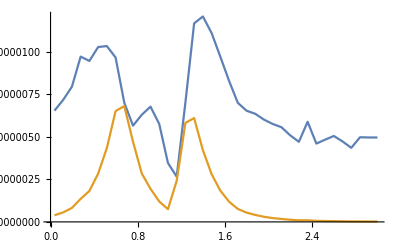

```mathematica
ListLinePlot[{DTshsp2[[All,{1,2}]],DTshsp2[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 3

```mathematica
Remove[x11,DTshsp3];
```

```mathematica
x11 = 1;
listDTshsp3=ParallelTable[
   Z=Vthsp3s[[x11]][[1]];
   V=Vthsp3s[[x11]][[2]]; (* 0.1 *)
   Dshsp31=NIntegrate[Sshc31s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   Dshsp32=NIntegrate[Sshc32s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp31,Dshsp32}, 
   {x11,1,38,1}];
DTshsp3=SortBy[listDTshsp3,First]
```

{{0.04,1.489294529×10^-6,5.461290885×10^-7},{0.12,1.592188646×10^-6,7.064687945×10^-7},{0.2,1.723994732×10^-6,8.837395707×10^-7},{0.28,1.890123016×10^-6,1.062334981×10^-6},{0.36,2.083617512×10^-6,1.237044024×10^-6},{0.44,2.305079919×10^-6,1.471796946×10^-6},{0.52,2.323764962×10^-6,1.791552203×10^-6},{0.6,1.989886678×10^-6,2.186776451×10^-6},{0.68,1.466783043×10^-6,2.249791874×10^-6},{0.76,1.216887262×10^-6,1.613446228×10^-6},{0.84,1.342646451×10^-6,1.004317301×10^-6},{0.92,1.892382612×10^-6,9.133327306×10^-7},{1.,1.324998993×10^-6,5.301984762×10^-7},{1.08,1.328807277×10^-6,6.812494578×10^-7},{1.16,8.173691144×10^-7,9.734771278×10^-7},{1.24,1.566951333×10^-6,1.331570736×10^-6},{1.32,3.436764545×10^-6,1.467403449×10^-6},{1.4,3.686775086×10^-6,7.629164651×10^-7},{1.48,2.290475852×10^-6,2.498120408×10^-7},{1.56,2.081643644×10^-6,1.356132388×10^-7},{1.64,1.786642538×10^-6,7.798953326×10^-8},{1.72,1.826065184×10^-6,5.816249167×10^-8},{1.8,1.741387095×10^-6,4.283137396×10^-8},{1.88,1.722849875×10^-6,3.392592427×10^-8},{1.96,1.744164955×10^-6,2.814173971×10^-8},{2.04,1.205263355×10^-6,1.618296257×10^-8},{2.12,1.167536121×10^-6,1.319049617×10^-8},{2.2,1.289361953×10^-6,1.236073385×10^-8},{2.28,1.300034099×10^-6,1.064826197×10^-8},{2.36,1.266813735×10^-6,8.917336199×10^-9},{2.44,1.20693548×10^-6,7.339406586×10^-9},{2.52,1.154888284×10^-6,6.095704476×10^-9},{2.6,9.966565614×10^-7,4.586009093×10^-9},{2.68,1.693050394×10^-6,6.819346399×10^-9},{2.76,9.589709801×10^-7,3.394150967×10^-9},{2.84,1.274351862×10^-6,3.977892507×10^-9},{2.92,9.567244988×10^-7,2.642950886×10^-9},{3.,1.268356469×10^-6,3.111087178×10^-9}}

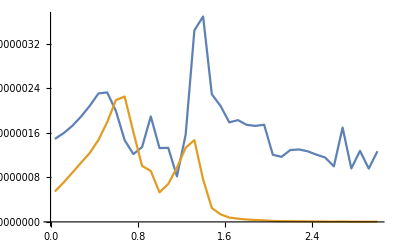

```mathematica
ListLinePlot[{DTshsp3[[All,{1,2}]],DTshsp3[[All,{1,3}]]},PlotRange->All]
```

### Spin-configuration 4

```mathematica
Remove[x11,DTshsp4];
```

```mathematica
x11 = 1;
listDTshsp4=ParallelTable[
   Z=Vthsp4s[[x11]][[1]];
   V=Vthsp4s[[x11]][[2]]; 
   Dshsp4=NIntegrate[Sshc4s,{Ed,-∞, ∞},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion-> 50,WorkingPrecision->10];
   {Z,Dshsp4}, 
   {x11,1,38,1}];
DTshsp4=SortBy[listDTshsp4,First](*Sort based on Z values*)
```

{{0.04,3.572644066×10^-7},{0.12,4.597907847×10^-7},{0.2,5.679199227×10^-7},{0.28,6.632507665×10^-7},{0.36,7.328969216×10^-7},{0.44,7.459747787×10^-7},{0.52,7.159298047×10^-7},{0.6,6.427833334×10^-7},{0.68,5.670558316×10^-7},{0.76,4.332638127×10^-7},{0.84,3.374425606×10^-7},{0.92,2.524156814×10^-7},{1.,1.886960314×10^-7},{1.08,1.408742785×10^-7},{1.16,1.05298097×10^-7},{1.24,8.128863197×10^-8},{1.32,6.073367403×10^-8},{1.4,5.182332775×10^-8},{1.48,4.076736277×10^-8},{1.56,2.941500702×10^-8},{1.64,2.71377181×10^-8},{1.72,1.844658005×10^-8},{1.8,1.772295923×10^-8},{1.88,1.290725298×10^-8},{1.96,9.969974676×10^-9},{2.04,9.977827935×10^-9},{2.12,7.967435948×10^-9},{2.2,7.138692981×10^-9},{2.28,5.458883155×10^-9},{2.36,4.532356427×10^-9},{2.44,4.009626353×10^-9},{2.52,3.280447548×10^-9},{2.6,2.941860375×10^-9},{2.68,2.61759521×10^-9},{2.76,3.383493384×10^-9},{2.84,1.840302216×10^-9},{2.92,1.647997868×10^-9},{3.,1.584052312×10^-9}}

```mathematica
ListLinePlot[{DTshsp4[[All,{1,2}]]},PlotRange->All]
```

-Graphics-

```mathematica
DlTsh=ParallelTable[Flatten[{DTshsp1[[pp]][[1]],DTshsp1[[pp]][[2]]+DTshsp4[[pp]][[2]]+DTshsp2[[pp]][[2]]+DTshsp3[[pp]][[2]],(DTshsp2[[pp]][[3]]+DTshsp3[[pp]][[3]]),DTshsp1[[pp]][[2]]+DTshsp4[[pp]][[2]]+DTshsp2[[pp]][[2]]+DTshsp3[[pp]][[2]]-(DTshsp2[[pp]][[3]]+DTshsp3[[pp]][[3]])}],{pp,1,38,1}]
```

{{0.036,3.853352235×10^-6,5.850408074×10^-7,3.26831143×10^-6},{0.116,4.515246289×10^-6,7.623617205×10^-7,3.75288457×10^-6},{0.196,5.248160597×10^-6,9.659075595×10^-7,4.28225304×10^-6},{0.276,6.050321482×10^-6,1.197775478×10^-6,4.852546×10^-6},{0.356,6.556385475×10^-6,1.41896466×10^-6,5.13742082×10^-6},{0.436,6.932990712×10^-6,1.755009151×10^-6,5.17798156×10^-6},{0.516,6.818932568×10^-6,2.225186169×10^-6,4.5937464×10^-6},{0.596,6.07921354×10^-6,2.837945897×10^-6,3.24126764×10^-6},{0.676,4.798547585×10^-6,2.930483073×10^-6,1.86806451×10^-6},{0.756,3.898121519×10^-6,2.084429576×10^-6,1.81369194×10^-6},{0.836,3.610371446×10^-6,1.289067802×10^-6,2.32130364×10^-6},{0.916,3.994534022×10^-6,1.10810926×10^-6,2.88642476×10^-6},{0.996,2.813681624×10^-6,6.503979127×10^-7,2.16328371×10^-6},{1.076,2.35667966×10^-6,7.560015472×10^-7,1.60067811×10^-6},{1.156,1.593926142×10^-6,1.214373058×10^-6,3.79553084×10^-7},{1.236,2.671383886×10^-6,1.913262123×10^-6,7.58121762×10^-7},{1.316,4.901412676×10^-6,2.077628093×10^-6,2.82378458×10^-6},{1.396,5.128283641×10^-6,1.18514263×10^-6,3.94314101×10^-6},{1.476,3.589542767×10^-6,5.303184353×10^-7,3.05922433×10^-6},{1.556,3.262146482×10^-6,3.194182061×10^-7,2.94272828×10^-6},{1.636,2.776704861×10^-6,1.96874541×10^-7,2.57983032×10^-6},{1.716,2.614514515×10^-6,1.34573673×10^-7,2.47994084×10^-6},{1.796,2.473404449×10^-6,9.742205732×10^-8,2.37598239×10^-6},{1.876,2.433753235×10^-6,7.479723446×10^-8,2.358956×10^-6},{1.956,2.40558633×10^-6,5.816833307×10^-8,2.347418×10^-6},{2.036,1.822835778×10^-6,3.871117222×10^-8,1.78412461×10^-6},{2.116,1.758650769×10^-6,3.041669166×10^-8,1.72823408×10^-6},{2.196,1.826931936×10^-6,2.493826662×10^-8,1.80199367×10^-6},{2.276,1.795874037×10^-6,2.002097703×10^-8,1.77585306×10^-6},{2.356,1.888877372×10^-6,1.844228206×10^-8,1.87043509×10^-6},{2.436,1.690409495×10^-6,1.344635478×10^-8,1.67696314×10^-6},{2.516,1.654909179×10^-6,1.13931173×10^-8,1.64351606×10^-6},{2.596,1.51491631×10^-6,9.197008345×10^-9,1.5057193×10^-6},{2.676,2.180894893×10^-6,1.044055366×10^-8,2.17045434×10^-6},{2.756,1.408443999×10^-6,6.207372047×10^-9,1.40223663×10^-6},{2.836,1.78451001×10^-6,6.709185361×10^-9,1.77780083×10^-6},{2.916,1.463853508×10^-6,4.970938811×10^-9,1.45888257×10^-6},{2.996,1.771815671×10^-6,5.11044063×10^-9,1.76670523×10^-6}}

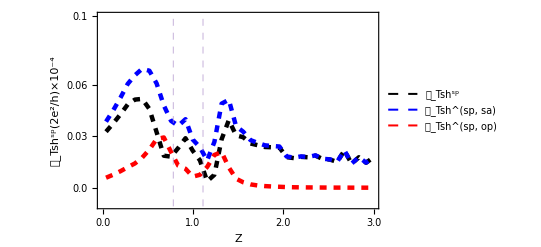

```mathematica
DSsh=ListLinePlot[{DlTsh[[All,{1,4}]],DlTsh[[All,{1,2}]],DlTsh[[All,{1,3}]]},PlotRange->{-0.000001,0.00001},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^sp(2e^2/h)×10^-4",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.000003,"0.03"},{0.00001,"0.1"},{0.000006,"0.06"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tsh^(sp, sa)",16,Bold],Style["𝒟_Tsh^(sp, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

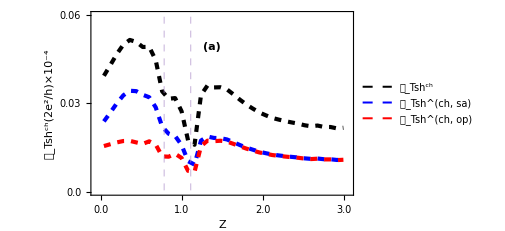

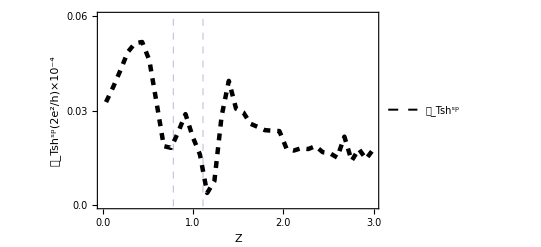

```mathematica
ListLinePlot[{DlTsh[[All,{1,4}]]},PlotRange->{-0.00,0.000006},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^sp(2e^2/h)×10^-4",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.000003,"0.03"},{0.00001,"0.1"},{0.000006,"0.06"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tsh^(ch, sa)",16,Bold],Style["𝒟_Tsh^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

```mathematica
DlTsp=ParallelTable[Flatten[{DlTth[[pp]][[1]],DlTth[[pp]][[2]]+DlTsh[[pp]][[2]],DlTth[[pp]][[3]]+DlTsh[[pp]][[3]],DlTth[[pp]][[4]]+DlTsh[[pp]][[4]],(DlTsh[[pp]][[4]]/(DlTth[[pp]][[4]]))}],{pp,1,38,1}]
```

{{0.036,0.0002811124608,-0.000192331399,0.00047344386,0.00695125775},{0.116,0.000325670723,-0.000205623274,0.000531293997,0.00711391867},{0.196,0.0003826785611,-0.000222138416,0.000604816977,0.00713073343},{0.276,0.0004543610392,-0.00024305257,0.000697413609,0.00700666881},{0.356,0.0005397891334,-0.000266296833,0.000806085966,0.00641417085},{0.436,0.0006478682886,-0.000291679419,0.000939547708,0.00554168379},{0.516,0.0007868659163,-0.000308456529,0.00109532244,0.00421163063},{0.596,0.0009581764003,-0.000295020649,0.00125319705,0.00259310584},{0.676,0.001113325568,-0.000223900825,0.00133722639,0.00139892377},{0.756,0.001174618496,-0.000106101611,0.00128072011,0.00141815845},{0.836,0.001146718574,2.73088765×10^-6,0.00114398769,0.00203325917},{0.916,0.001125309281,0.00006745109082,0.00105785819,0.00273602087},{0.996,0.001135597542,0.00008130468875,0.00105429285,0.0020561001},{1.076,0.001217258917,0.00004217633046,0.00117508259,0.00136404158},{1.156,0.001203356455,-0.0000565352825,0.00125989174,0.000301349275},{1.236,0.001035459209,-0.000166884268,0.00120234348,0.000630934589},{1.316,0.0007920329963,-0.000230310678,0.00102234367,0.00276971996},{1.396,0.0005710642349,-0.00024008366,0.000811147895,0.00488493284},{1.476,0.0004164239033,-0.00022422421,0.000640648113,0.00479811425},{1.556,0.000324673059,-0.000206577448,0.000531250507,0.00557010212},{1.636,0.0002654104946,-0.000189807125,0.00045521762,0.00569954692},{1.716,0.0002275711682,-0.00017665433,0.000404225498,0.00617291417},{1.796,0.0002017566213,-0.000165996305,0.000367752927,0.00650282518},{1.876,0.00018388103,-0.000157725213,0.000341606243,0.00695349997},{1.956,0.0001708148246,-0.000151055366,0.00032187019,0.00734663755},{2.036,0.0001584650503,-0.0001438064,0.000302271451,0.00593743712},{2.116,0.0001508125441,-0.000139256693,0.000290069237,0.00599371597},{2.196,0.0001453143607,-0.000135856086,0.000281170447,0.00645024035},{2.276,0.0001405100278,-0.000132691434,0.000273201462,0.00654268796},{2.356,0.0001376269148,-0.00013087302,0.000268499935,0.00701510931},{2.436,0.0001333608503,-0.000127759042,0.000261119892,0.00646370725},{2.516,0.0001308228278,-0.000125965828,0.000256788656,0.00644149469},{2.596,0.0001281597755,-0.000124003697,0.000252163472,0.00600707253},{2.676,0.0001291818776,-0.000124756136,0.000253938014,0.00862086578},{2.756,0.0001242320018,-0.000120964555,0.000245196557,0.00575171983},{2.836,0.0001249172144,-0.000121539628,0.000246456842,0.00726584842},{2.916,0.0001223448403,-0.000119531511,0.000241876351,0.00606812217},{2.996,0.0001228300098,-0.000119891689,0.000242721699,0.00733209636}}

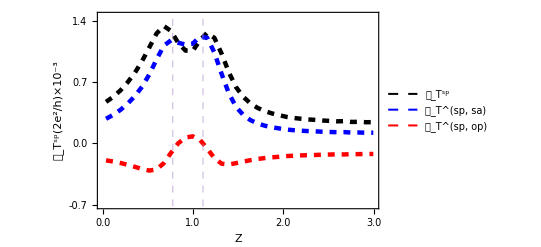

```mathematica
Dch=ListLinePlot[{DlTsp[[All,{1,4}]],DlTsp[[All,{1,2}]],DlTsp[[All,{1,3}]]},PlotRange->{-0.0007,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^sp",16,Bold],Style["𝒟_T^(sp, sa)",16,Bold],Style["𝒟_T^(sp, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

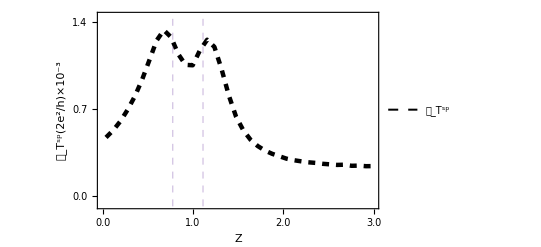

```mathematica
ListLinePlot[{DlTsp[[All,{1,4}]]},PlotRange->{-0.00007,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^sp",16,Bold],Style["𝒟_T^(ch, sa)",16,Bold],Style["𝒟_T^(ch, op)",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

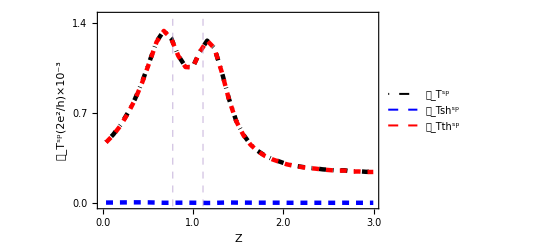

```mathematica
ListLinePlot[{DlTsp[[All,{1,4}]],DlTsh[[All,{1,4}]],DlTth[[All,{1,4}]]},PlotRange->{-0.000015,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^sp",16,Bold],Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tth^sp",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

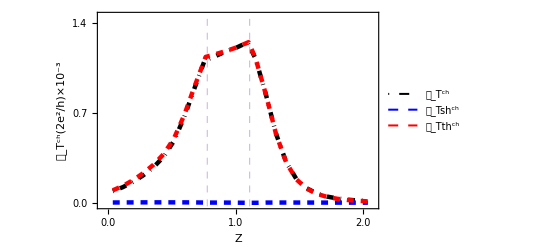

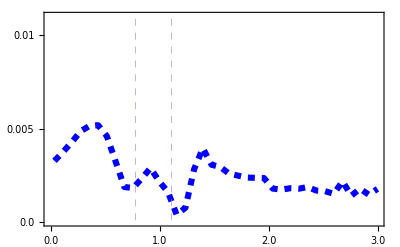

```mathematica
Dsh=ListLinePlot[{DlTsh[[All,{1,4}]]},PlotRange->{-0.00,0.000011},GridLines-> {{0.78,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Directive[Pink,Thickness[0.006]],Axes->False,PlotStyle->{{Blue,Dashed,Thickness[0.011]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,13,Bold],FrameLabel-> {Style["",22,Black,Bold,FontSlant->Italic],Style["",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{0.00003,"0.03"},{0.00001,"0.01"},{0.000005,"0.005"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,15,Black}]
```

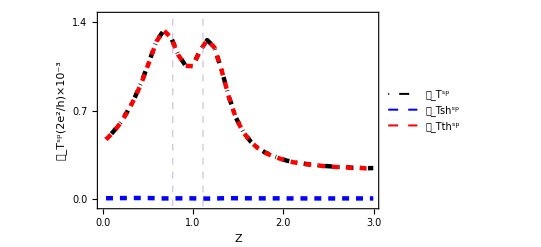

```mathematica
xyMinMax={{0.02,2.001},{-.00002,0.00005}};

ListLinePlot[{DlTsp[[All,{1,4}]],DlTsh[[All,{1,4}]],DlTth[[All,{1,4}]]},PlotRange->{-0.00005,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^sp",16,Bold],Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tth^sp",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

```mathematica
DlTsp[[All,{1,5}]]
```

{{0.036,0.00567961948},{0.116,0.00584640955},{0.196,0.00582779115},{0.276,0.00558302715},{0.356,0.00505854339},{0.436,0.00443119658},{0.516,0.00401630383},{0.596,0.00407351188},{0.676,0.00410647046},{0.756,0.0037300369},{0.836,0.00346946215},{0.916,0.00375644844},{0.996,0.00259059989},{1.076,0.00214145845},{1.156,0.00195371677},{1.236,0.00295227159},{1.316,0.00371890716},{1.396,0.00320241606},{1.476,0.00259189099},{1.556,0.00302323474},{1.636,0.00325277272},{1.716,0.00366029024},{1.796,0.00406899841},{1.876,0.00454404521},{1.956,0.00494993262},{2.036,0.00411614541},{2.116,0.00423568237},{2.196,0.00462259927},{2.276,0.00474811754},{2.356,0.00515834701},{2.436,0.00478603775},{2.516,0.0048000656},{2.596,0.00450321696},{2.676,0.00648838697},{2.756,0.00435506392},{2.836,0.0055165511},{2.916,0.00462367994},{2.996,0.00559607296}}

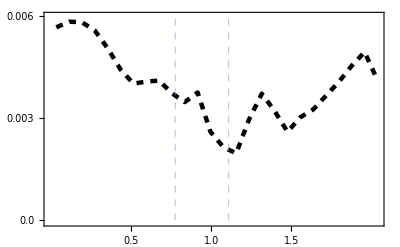

```mathematica
Pshth1=ListLinePlot[{DlTsps[[All,{1,5}]]},PlotRange->{-0.00007,.006},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,14,Bold],FrameLabel-> {Style["",22,Black,Bold,FontSlant->Italic],Style["",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.006,"0.006"},{0.003,"0.003"},{2.14,"2.14"},{0.0,"0.0"}},None},{{{0.5,"0.5"},{1,"1.0"},{1.5,"1.5"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

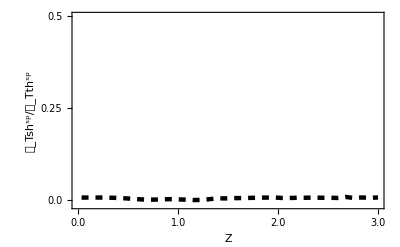

```mathematica
xyMinMax={{1.6,.4},{-.0123,.017}};

PDshth=ListLinePlot[{DlTsp[[All,{1,5}]]},PlotRange->{-0.013,.5},Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^sp/𝒟_Tth^sp",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.5,"0.5"},{0.25,"0.25"},{2.14,"2.14"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large},Epilog->{Transparent,EdgeForm[{Red,Thick}],Rectangle[Sequence@@Transpose[xyMinMax]],Inset[Pshth1,Scaled[{.16,.52}],Scaled[{0,0}],2.4],PlotRange->{-0.2,0.003},PlotRangeClipping->False}]
```

## Plots till Z=2

```mathematica
(* Charge: DlTthcs=DlTthc, till Z=2 *)
```

```mathematica
DlTthc
```

```mathematica
DlTthcs={{0.036,0.00028746874362461016988535972525790985`10.,-0.00019050542998959213439704349877122451`10.,0.00009696331363501803548831622648668534`9.307203017697814},{0.11599999999999999,0.00033529142379992439176633604959640927`10.,-0.00020374680113405734100659894681864368`10.,0.00013154462266586705075973710277776559`9.387453536022525},{0.196,0.00039604364935612529907256981326792221`10.,-0.00022019177852443577740401561535616408`10.,0.00017585187083168952166855419791175813`9.455400330352433},{0.27599999999999997,0.00047079606360885866407888111960369907`10.,-0.00024072504707835423669802050383236278`10.,0.00023007101653050442738086061577133629`9.50967412131068},{0.35600000000000004,0.00055893207908886802379709721487125381`10.,-0.0002642721666969848409163350713871612`10.,0.00029465991239188318288076214348409261`9.553813453699126},{0.43600000000000005,0.00066639065278085757792257912159260633`10.,-0.00028958933674334275173233763348864461`10.,0.00037680131603751482619024148810396172`9.59566360920151},{0.516,0.00080202145437627713489819429354034865`10.,-0.00030674856193701165752676946518382338`10.,0.00049527289243926547737142482835652527`9.650003085470926},{0.596,0.0009672438293090307796565731025507105`10.,-0.00029398320684951633862316754007384272`10.,0.00067326062245951444103340556247686778`9.727389942393986},{0.676,0.00111591136434543664119556488811456827`10.,-0.00022382369369093941838943151322791035`10.,0.00089208767065449722280613337488665792`9.823388615034114},{0.756,0.00117197668459617561066991961668861949`10.,-0.00010674725462052756124317392753904409`10.,0.0010652294299756480494267456891495754`9.920666360789365},{0.836,0.00114078390346644528696168467480752684`10.,1.4020871868578978156869192086982`9.80176652734962*^-6,0.00114218599065330318477737159401622504`9.999691722809048},{0.916,0.00111078036030069658360960007168989061`10.,0.0000651537458594785736420517905841148`10.,0.00117593410616017515725165186227400541`10.},{0.9960000000000001,0.00112274179288351388320994582370376634`10.,0.00007944664859132274536332034287118985`10.,0.00120218844147483662857326616657495619`10.},{1.076,0.00119029595078739534132382111452458828`10.,0.0000404337437345824819004680528640425`10.,0.00123072969452197782322428916738863078`10.},{1.1560000000000001,0.001184425243895006099712062512664886`10.,-0.00005668444347651389326424526754798043`10.,0.00112774080041849220644781724511690557`9.958399127537685},{1.236,0.00102255816850442302363812944680269096`10.,-0.00016662994522274386451002459657641285`10.,0.00085592822328167915912810485022627811`9.857186787332665},{1.316,0.0007749291399791583262396833844027685`10.,-0.00022809036280318188658154689174837879`10.,0.00054683877717597643965813649265438971`9.736549925920002},{1.3960000000000001,0.00055706994987813057597162575191813996`10.,-0.00023674144913463029638311204967881568`10.,0.00032032850074350027958851370223932428`9.60587825005748},{1.476,0.00040865843262087514796123447756332682`10.,-0.00022177955260345919394924547419457185`10.,0.00018687888001741595401198900336875497`9.47191785024018},{1.556,0.0003178177428473400247288360632471678`10.,-0.00020396963761057189580651372606463799`10.,0.00011384810523676812892232233718252981`9.33883223570534},{1.6360000000000001,0.00025981406355319705315328474232089877`10.,-0.0001874222931720631592981107508333768`10.,0.00007239177038113389385517399148752197`9.209152096704004},{1.7160000000000002,0.00022223461739549452204475052444752538`10.,-0.00017412945100509588844890269483775833`10.,0.00004810516639039863359584782960976705`9.084097443671103},{1.7960000000000003,0.00019660352433921163892213505317401581`10.,-0.00016342444450390909421558173034358861`10.,0.0000331790798353025447065533228304272`8.964528097115526},{1.8760000000000003,0.00017866063165664704407632517004321444`10.,-0.00015500988541135366673398342687953996`10.,0.00002365074624529337734234174316367448`8.850527014117441},{1.956,0.00016557556245896600254212284259946061`10.,-0.00014825323907068642389938705031798517`10.,0.00001732232338827957864273579228147544`8.74191334382343},{2.036,0.00015477089785610304515401632967325429`10.,-0.00014185796385051816886715528752944679`10.,0.0000129129340055848762868610421438075`8.638811526284492}}
```

{{0.036,0.0002874687436,-0.00019050543,0.0000969633136},{0.116,0.0003352914238,-0.0002037468011,0.000131544623},{0.196,0.0003960436494,-0.0002201917785,0.000175851871},{0.276,0.0004707960636,-0.0002407250471,0.000230071017},{0.356,0.0005589320791,-0.0002642721667,0.000294659912},{0.436,0.0006663906528,-0.0002895893367,0.000376801316},{0.516,0.0008020214544,-0.0003067485619,0.000495272892},{0.596,0.0009672438293,-0.0002939832068,0.000673260622},{0.676,0.001115911364,-0.0002238236937,0.000892087671},{0.756,0.001171976685,-0.0001067472546,0.00106522943},{0.836,0.001140783903,1.40208719×10^-6,0.00114218599},{0.916,0.00111078036,0.00006515374586,0.001175934106},{0.996,0.001122741793,0.00007944664859,0.001202188441},{1.076,0.001190295951,0.00004043374373,0.001230729695},{1.156,0.001184425244,-0.00005668444348,0.0011277408},{1.236,0.001022558169,-0.0001666299452,0.000855928223},{1.316,0.00077492914,-0.0002280903628,0.000546838777},{1.396,0.0005570699499,-0.0002367414491,0.000320328501},{1.476,0.0004086584326,-0.0002217795526,0.00018687888},{1.556,0.0003178177428,-0.0002039696376,0.000113848105},{1.636,0.0002598140636,-0.0001874222932,0.0000723917704},{1.716,0.0002222346174,-0.000174129451,0.0000481051664},{1.796,0.0001966035243,-0.0001634244445,0.00003317908},{1.876,0.0001786606317,-0.0001550098854,0.000023650746},{1.956,0.0001655755625,-0.0001482532391,0.000017322323},{2.036,0.0001547708979,-0.0001418579639,0.000012912934}}

```mathematica
(* SPin: DlTths=DlTth,    till Z=2 *)
```

```mathematica
DlTth
```

```mathematica
DlTths={{0.036,0.00027725910853357252785384220035827966`10.,-0.00019291644009905070745542400186248941`10.,0.00047017554863262323530926620222076907`10.},{0.11599999999999999,0.00032115547669766550028551493914545776`10.,-0.00020638563595602343727105981553840335`10.,0.00052754111265368893755657475468386111`10.},{0.196,0.0003774304004653339108334396810180804`10.,-0.00022310432391677143147872750780605977`10.,0.00060053472438210534231216718882414017`10.},{0.27599999999999997,0.0004483107176898390346021761517443609`10.,-0.00024425034559562835589168342499369024`10.,0.00069256106328546739049385957673805114`10.},{0.35600000000000004,0.00053323274796331268123104066997116049`10.,-0.00026771579766970370043044290300996132`10.,0.00080094854563301638166148357298112181`10.},{0.43600000000000005,0.00064093529790270422988371370266335822`10.,-0.00029343442809839367286222250357980156`10.,0.00093436972600109790274593620624315978`10.},{0.516,0.00078004698377930514422517642173048029`10.,-0.0003106817147837921633439109786681133`10.,0.00109072869856309730756908740039859359`10.},{0.596,0.00095209718675792291770631924768269362`10.,-0.00029785859510857172866520089245583993`10.,0.00124995578186649464637152014013853355`10.},{0.676,0.00110852701998054582102587069073542934`10.,-0.00022683130851305641743687401400049312`10.,0.00133535832849360223846274470473592246`10.},{0.756,0.0011707203747181971875414455846196961`10.,-0.0001081860405905988116868983655842951`10.,0.0012789064153087959992283439502039912`10.},{0.836,0.00114310820249596694358483174716712437`10.,1.44181984566976698361784950229411`9.805684966840673*^-6,0.00114166638265029717660121389766483026`9.99859583029779},{0.916,0.00112131474651082973197638313769145801`10.,0.00006634298156040984178928086482414787`10.,0.00105497176495041989018710227286731014`9.948549537380377},{0.9960000000000001,0.00113278386009278345381592176410391021`10.,0.00008065429083341192955638029621053989`10.,0.00105212956925937152425954146789337032`9.938051581076113},{1.076,0.00121490223752712028036799219317725368`10.,0.00004142032891426985727932637939497807`10.,0.00117348190861285042308866581378227561`9.97037523776565},{1.1560000000000001,0.00120176252840388184403600674807030562`10.,-0.00005774965559249964586518029275355449`10.,0.00125951218399638148990118704082386011`10.},{1.236,0.00103278782535760925412414538492449341`10.,-0.00016879753011190747689984064594807945`10.,0.00120158535546951673102398603087257286`10.},{1.316,0.00078713158358512645333635442239001421`10.,-0.00023238830606254956556237704685484299`10.,0.0010195198896476760188987314692448572`10.},{1.3960000000000001,0.00056593595125786473895188771422156479`10.,-0.00024126880228263180992972833932873718`10.,0.00080720475354049654888161605355030197`10.},{1.476,0.0004128343605487591814310853139405939`10.,-0.00022475452803635024291750137447969903`10.,0.00063758888858510942434858668842029293`10.},{1.556,0.00032141091256631299453636289551642731`10.,-0.00020689686575816982464633115421474237`10.,0.00052830777832448281918269404973116968`10.},{1.6360000000000001,0.00026263378973112207796826838441755238`10.,-0.0001900039998964548010936235274592245`10.,0.00045263778962757687906189191187677688`10.},{1.7160000000000002,0.00022495665368899578878802029226840571`10.,-0.00017678890323464312026508835670612196`10.,0.00040174555692363890905310864897452767`10.},{1.7960000000000003,0.00019928321688987755944030036202683787`10.,-0.00016609372734282279696385382431512148`10.,0.00036537694423270035640415418634195935`10.},{1.8760000000000003,0.00018144727672251116811913980791462526`10.,-0.0001578000102508252492885577231776879`10.,0.00033924728697333641740769753109231316`10.},{1.956,0.00016840923829154435789144767463438556`10.,-0.00015111353395828152148023509314324982`10.,0.00031952277224982587937168276777763538`10.},{2.036,0.00015664221452212039482627605613694632`10.,-0.00014384511164391508174548468841183648`10.,0.0003004873261660354765717607445487828`10.}}
```

{{0.036,0.0002772591085,-0.0001929164401,0.0004701755486},{0.116,0.0003211554767,-0.000206385636,0.0005275411127},{0.196,0.0003774304005,-0.0002231043239,0.0006005347244},{0.276,0.0004483107177,-0.0002442503456,0.0006925610633},{0.356,0.000533232748,-0.0002677157977,0.0008009485456},{0.436,0.0006409352979,-0.0002934344281,0.000934369726},{0.516,0.0007800469838,-0.0003106817148,0.001090728699},{0.596,0.0009520971868,-0.0002978585951,0.001249955782},{0.676,0.00110852702,-0.0002268313085,0.001335358328},{0.756,0.001170720375,-0.0001081860406,0.001278906415},{0.836,0.001143108202,1.44181985×10^-6,0.00114166638},{0.916,0.001121314747,0.00006634298156,0.00105497176},{0.996,0.00113278386,0.00008065429083,0.00105212957},{1.076,0.001214902238,0.00004142032891,0.00117348191},{1.156,0.001201762528,-0.00005774965559,0.001259512184},{1.236,0.001032787825,-0.0001687975301,0.001201585355},{1.316,0.0007871315836,-0.0002323883061,0.00101951989},{1.396,0.0005659359513,-0.0002412688023,0.0008072047535},{1.476,0.0004128343605,-0.000224754528,0.0006375888886},{1.556,0.0003214109126,-0.0002068968658,0.0005283077783},{1.636,0.0002626337897,-0.0001900039999,0.0004526377896},{1.716,0.0002249566537,-0.0001767889032,0.0004017455569},{1.796,0.0001992832169,-0.0001660937273,0.0003653769442},{1.876,0.0001814472767,-0.0001578000103,0.000339247287},{1.956,0.0001684092383,-0.000151113534,0.0003195227722},{2.036,0.0001566422145,-0.0001438451116,0.0003004873262}}

```mathematica
(* Charge DlTshcs=DlTshc,   till Z=2 *)
```

```mathematica
DlTshcs={{0.036,2.70227281468149801489854566285596`10.*^-6,4.2500656502226076211371233708632`10.*^-7,3.12727937970375877701225799994228`10.*^-6},{0.11599999999999999,3.04608997010591071807642618703697`10.*^-6,5.5646556928400231785937323411934`10.*^-7,3.60255553938991303593579942115631`10.*^-6},{0.196,3.43978445011474522917153413012636`10.*^-6,7.1180469325626841353452834127283`10.*^-7,4.15158914337101364270606247139919`10.*^-6},{0.27599999999999997,3.85362211957801922828844712211053`10.*^-6,8.8854918121472967830112589130353`10.*^-7,4.74217130079274890658957301341406`10.*^-6},{0.35600000000000004,4.25022605254604373640224343335409`10.*^-6,1.09757383042798772036100674692807`10.*^-6,5.34779988297403145676325018028216`10.*^-6},{0.43600000000000005,4.54346523340967671192829973976405`10.*^-6,1.39768601985877761420101687059111`10.*^-6,5.94115125326845432612931661035516`10.*^-6},{0.516,4.54467732578947111320154924254677`10.*^-6,1.85125967467415855954098946945376`10.*^-6,6.39593700046362967274253871200053`10.*^-6},{0.596,4.00840043454827568608817134839764`10.*^-6,2.40213054152637747636677423823`10.*^-6,6.41053097607465316245494558662764`10.*^-6},{0.676,3.08999566955690356504065598964259`10.*^-6,2.47322101542437812225623447080127`10.*^-6,5.56321668498128168729689046044386`10.*^-6},{0.756,2.48609192289408649002792693282233`10.*^-6,1.74215303958027026072443251288974`10.*^-6,4.22824496247435675075235944571207`10.*^-6},{0.836,2.47652731960326084084435663441174`10.*^-6,1.08004081505908613568766572807668`10.*^-6,3.55656813466234697653202236248842`10.*^-6},{0.916,2.61786441439186694749679935832982`10.*^-6,8.2216444843508347135192077078649`10.*^-7,3.44002886282695041884872012911631`10.*^-6},{0.9960000000000001,2.04366445765987521177424642844198`10.*^-6,5.0981782955342562129472202760949`10.*^-7,2.55348228721330083306896845605147`10.*^-6},{1.076,1.44820671831071034392283981189205`10.*^-6,4.5471054193854963312798648013134`10.*^-7,1.90291726024925997705082629202339`10.*^-6},{1.1560000000000001,1.08786976759718238989544082327525`10.*^-6,9.3088227804011215861528316515683`10.*^-7,2.01875204563729454851072398843208`10.*^-6},{1.236,2.24874232418365948807466972492056`10.*^-6,1.75050782253908026655994777587071`10.*^-6,3.99925014672273975463461750079127`10.*^-6},{1.316,3.79988476540040971979135768285972`10.*^-6,1.72933732677239960338033360698332`10.*^-6,5.52922209217280932317169128984304`10.*^-6},{1.3960000000000001,3.98215799065747754391013382193116`10.*^-6,1.05269796342674573657463081003837`10.*^-6,5.03485595408422328048476463196953`10.*^-6},{1.476,3.18563826529238137546876282108563`10.*^-6,5.6369608515327595723726141326642`10.*^-7,3.74933435044565733270602423435205`10.*^-6},{1.556,2.78932854865987252296805933795381`10.*^-6,3.4555480409168952981804122101311`10.*^-7,3.13488335275156205278610055896692`10.*^-6},{1.6360000000000001,2.42221756810942321573994312267886`10.*^-6,2.2123413129660606034302555849219`10.*^-7,2.64345169940602927608296868117105`10.*^-6},{1.7160000000000002,2.23485752216017824238726601601333`10.*^-6,1.5136233013483056540261727222411`10.*^-7,2.38621985229500880778988328823744`10.*^-6},{1.7960000000000003,2.06547494644580608396929359635153`10.*^-6,1.0655770080541425949964974632854`10.*^-7,2.17203264725122034346894334268007`10.*^-6},{1.8760000000000003,1.95127391561345475566533079344461`10.*^-6,7.766926783128086521747986298818`10.*^-8,2.02894318344473562088281065643279`10.*^-6},{1.956,1.86892387384253720188550760709737`10.*^-6,5.790996147951310125152831995629`10.*^-8,1.92683383532205030313703592705366`10.*^-6},{2.036,1.62566098083180950349161865137026`10.*^-6,4.226031582857977609557893093033`10.*^-8,1.66792129666038927958719758230059`10.*^-6}}
```

{{0.036,2.702272815×10^-6,4.25006565×10^-7,3.12727938×10^-6},{0.116,3.04608997×10^-6,5.564655693×10^-7,3.602555539×10^-6},{0.196,3.43978445×10^-6,7.118046933×10^-7,4.151589143×10^-6},{0.276,3.85362212×10^-6,8.885491812×10^-7,4.742171301×10^-6},{0.356,4.250226053×10^-6,1.09757383×10^-6,5.347799883×10^-6},{0.436,4.543465233×10^-6,1.39768602×10^-6,5.941151253×10^-6},{0.516,4.544677326×10^-6,1.851259675×10^-6,6.395937×10^-6},{0.596,4.008400435×10^-6,2.402130542×10^-6,6.410530976×10^-6},{0.676,3.08999567×10^-6,2.473221015×10^-6,5.563216685×10^-6},{0.756,2.486091923×10^-6,1.74215304×10^-6,4.228244962×10^-6},{0.836,2.47652732×10^-6,1.080040815×10^-6,3.556568135×10^-6},{0.916,2.617864414×10^-6,8.221644484×10^-7,3.440028863×10^-6},{0.996,2.043664458×10^-6,5.098178296×10^-7,2.553482287×10^-6},{1.076,1.448206718×10^-6,4.547105419×10^-7,1.90291726×10^-6},{1.156,1.087869768×10^-6,9.30882278×10^-7,2.018752046×10^-6},{1.236,2.248742324×10^-6,1.750507823×10^-6,3.999250147×10^-6},{1.316,3.799884765×10^-6,1.729337327×10^-6,5.529222092×10^-6},{1.396,3.982157991×10^-6,1.052697963×10^-6,5.034855954×10^-6},{1.476,3.185638265×10^-6,5.636960852×10^-7,3.74933435×10^-6},{1.556,2.789328549×10^-6,3.455548041×10^-7,3.134883353×10^-6},{1.636,2.422217568×10^-6,2.212341313×10^-7,2.643451699×10^-6},{1.716,2.234857522×10^-6,1.513623301×10^-7,2.386219852×10^-6},{1.796,2.065474946×10^-6,1.065577008×10^-7,2.172032647×10^-6},{1.876,1.951273916×10^-6,7.766926783×10^-8,2.028943183×10^-6},{1.956,1.868923874×10^-6,5.790996148×10^-8,1.926833835×10^-6},{2.036,1.625660981×10^-6,4.226031583×10^-8,1.667921297×10^-6}}

```mathematica
(* Spin DlTshs=DlTsh,   till Z=2 *)
```

```mathematica
DlTsh
```

```mathematica
DlTshs={{0.036,3.85335223509273508135653405434746`10.*^-6,5.8504080736827489786399358745575`10.*^-7,3.26831142772446018349254046689171`9.867097673866041*^-6},{0.11599999999999999,4.51524628895279086723143523061423`10.*^-6,7.6236172047025011003839254583047`10.*^-7,3.75288456848254075719304268478376`9.85192807638633*^-6},{0.196,5.24816059681543587439460092715966`10.*^-6,9.6590755950203512053006960410014`10.*^-7,4.28225303731340075386453132305952`9.83829631375811*^-6},{0.27599999999999997,6.05032148224374089541307696873805`10.*^-6,1.19777547838702399695703774560154`10.*^-6,4.85254600385671689845603922313651`9.825745666910663*^-6},{0.35600000000000004,6.55638547507747960553079499350826`10.*^-6,1.41896466007090549591478054705362`10.*^-6,5.13742081500657410961601444645464`9.808995382375661*^-6},{0.43600000000000005,6.9329907116110266578276244735739`10.*^-6,1.75500915070683625156016989876957`10.*^-6,5.17798156090419040626745457480433`9.775240694191165*^-6},{0.516,6.81893256787411010327489358289383`10.*^-6,2.22518616865597099325482949474771`10.*^-6,4.59374639921813911002006408814612`9.705800760624056*^-6},{0.596,6.07921353972180654840184152585411`10.*^-6,2.83794589692126842623490712856435`10.*^-6,3.24126764280053812216693439728976`9.560488361935477*^-6},{0.676,4.79854758455381232725771134226506`10.*^-6,2.93048307337839140144191424180241`10.*^-6,1.86806451117542092581579710046265`9.383266839975942*^-6},{0.756,3.89812151885353688286059084615538`10.*^-6,2.08442957574263098996998376658124`10.*^-6,1.81369194311090589289060707957414`9.48167710731762*^-6},{0.836,3.61037144634303131374442249123608`10.*^-6,1.28906780245295930478537443902079`10.*^-6,2.32130364389007200895904805221529`9.675585576191365*^-6},{0.916,3.99453402225105365125191041499334`10.*^-6,1.10810926022246744397685736239213`10.*^-6,2.88642476202858620727505305260121`9.752565033028821*^-6},{0.9960000000000001,2.81368162377808235871259334457945`10.*^-6,6.5039791273949291365420924115741`10.*^-7,2.16328371103858944505838410342204`9.795525625150884*^-6},{1.076,2.35667965993446592097012780951413`10.*^-6,7.5600154717086710409275825062698`10.*^-7,1.60067811276359881687736955888716`9.711169362933191*^-6},{1.1560000000000001,1.59392614244626752701838509916812`10.*^-6,1.21437305835260488249805775781942`10.*^-6,3.795530840936626445203273413487`9.13082914830746*^-7},{1.236,2.67138388574260950457350292549351`10.*^-6,1.91326212343616769734526468613028`10.*^-6,7.5812176230644180722823823936323`9.218433155035306*^-7},{1.316,4.90141267571280338950483038795025`10.*^-6,2.07762809271567792983880997694238`10.*^-6,2.82378458299712545966602041100787`9.607035827494963*^-6},{1.3960000000000001,5.12828364144905546152401703674787`10.*^-6,1.1851426295348578531600298666057`10.*^-6,3.94314101191419760836398717014217`9.79557719520774*^-6},{1.476,3.58954276741830709681011908066022`10.*^-6,5.303184352619280821391455388836`10.*^-7,3.05922433215637901467097354177662`9.870728739875041*^-6},{1.556,3.262146482317397196153863318002`10.*^-6,3.1941820607489426438132585450186`10.*^-7,2.94272827624250293177253746350014`9.914677362774801*^-6},{1.6360000000000001,2.77670486127893465000540918784043`10.*^-6,1.9687454098142753703317174010135`10.*^-7,2.57983032029750711297223744773908`9.938311602860969*^-6},{1.7160000000000002,2.61451451521961450017973344098799`10.*^-6,1.3457367300049880534305825565289`10.*^-7,2.4799408422191156948366751853351`9.955252649232053*^-6},{1.7960000000000003,2.47340444913705667946891897169526`10.*^-6,9.742205732398906982741013673304`10.*^-8,2.37598239181306760964150883496222`9.965770448757642*^-6},{1.8760000000000003,2.43375323496106747984154246671533`10.*^-6,7.479723446434470218925868216028`10.*^-8,2.35895600049672277765228378455505`9.973296997448562*^-6},{1.956,2.40558632974429846840037282442607`10.*^-6,5.816833306587535938458409179499`10.*^-8,2.34741799667842310901578873263108`9.978992970596968*^-6},{2.036,1.82283577791479262639151903080309`10.*^-6,3.871117221847251849114319998713`10.*^-8,1.78412460569632010790037583081596`9.981551188771315*^-6}}
```

{{0.036,3.853352235×10^-6,5.850408074×10^-7,3.26831143×10^-6},{0.116,4.515246289×10^-6,7.623617205×10^-7,3.75288457×10^-6},{0.196,5.248160597×10^-6,9.659075595×10^-7,4.28225304×10^-6},{0.276,6.050321482×10^-6,1.197775478×10^-6,4.852546×10^-6},{0.356,6.556385475×10^-6,1.41896466×10^-6,5.13742082×10^-6},{0.436,6.932990712×10^-6,1.755009151×10^-6,5.17798156×10^-6},{0.516,6.818932568×10^-6,2.225186169×10^-6,4.5937464×10^-6},{0.596,6.07921354×10^-6,2.837945897×10^-6,3.24126764×10^-6},{0.676,4.798547585×10^-6,2.930483073×10^-6,1.86806451×10^-6},{0.756,3.898121519×10^-6,2.084429576×10^-6,1.81369194×10^-6},{0.836,3.610371446×10^-6,1.289067802×10^-6,2.32130364×10^-6},{0.916,3.994534022×10^-6,1.10810926×10^-6,2.88642476×10^-6},{0.996,2.813681624×10^-6,6.503979127×10^-7,2.16328371×10^-6},{1.076,2.35667966×10^-6,7.560015472×10^-7,1.60067811×10^-6},{1.156,1.593926142×10^-6,1.214373058×10^-6,3.79553084×10^-7},{1.236,2.671383886×10^-6,1.913262123×10^-6,7.58121762×10^-7},{1.316,4.901412676×10^-6,2.077628093×10^-6,2.82378458×10^-6},{1.396,5.128283641×10^-6,1.18514263×10^-6,3.94314101×10^-6},{1.476,3.589542767×10^-6,5.303184353×10^-7,3.05922433×10^-6},{1.556,3.262146482×10^-6,3.194182061×10^-7,2.94272828×10^-6},{1.636,2.776704861×10^-6,1.96874541×10^-7,2.57983032×10^-6},{1.716,2.614514515×10^-6,1.34573673×10^-7,2.47994084×10^-6},{1.796,2.473404449×10^-6,9.742205732×10^-8,2.37598239×10^-6},{1.876,2.433753235×10^-6,7.479723446×10^-8,2.358956×10^-6},{1.956,2.40558633×10^-6,5.816833307×10^-8,2.347418×10^-6},{2.036,1.822835778×10^-6,3.871117222×10^-8,1.78412461×10^-6}}

```mathematica
(* Charge DlTchcs=DlTchc, till Z=2 *)
```

```mathematica
DlTchcs={{0.036,0.00029017101643929166790025827092076581`10.,-0.00019008042342456987363492978643413819`9.998062225184931,0.00010009059301472179426532848448662762`9.31815659382187,0.03225219170494963760512775535753036978`9.22698682213322},{0.11599999999999999,0.00033833751377003030248441247578344624`10.,-0.00020319033556477333868873957358452434`9.997627736723633,0.0001351471782052569637956729021989219`9.396294553614688,0.02738656637102276105234517567419176242`9.292620658819297},{0.196,0.00039948343380624004430174134739804857`10.,-0.00021947997383117950899048108701489125`9.997192139239957,0.00018000345997506053531126026038315732`9.46261815240778,0.02360844456039118423327383691258013433`9.346373943655756},{0.27599999999999997,0.0004746496857284366833071695667258096`10.,-0.00023983649789713950701971937794105925`9.996793904385715,0.00023481318783129717628745018878475035`9.515649796209763,0.02061177184464692713331690006777482789`9.387999092697237},{0.35600000000000004,0.0005631823051414140675334994583046079`10.,-0.00026317459286655685319597406464023313`9.996392559952703,0.00030000771227485721433752539366437477`9.558812625327258,0.01814905814490883573143917941990148767`9.420932023699535},{0.43600000000000005,0.00067093411801426725463450742133237038`10.,-0.0002881916507234839741181366166180535`9.995807773545334,0.00038274246729078328051637080471431688`9.59976718253928,0.01576733148319722329752486677509727188`9.451353518550071},{0.516,0.00080656613170206660601139584278289542`10.,-0.00030489730226233749896722847571436962`9.994757911055588,0.0005016688294397291070441673670685258`9.653077615840914,0.01291396540796537375006297458591895628`9.489628576932967},{0.596,0.00097125222974357905534266127389910814`10.,-0.00029158107630798996114680076583561272`9.992902620063248,0.00067967115343558909419586050806349542`9.729303736747552,0.00952161876429976598014142754676452114`9.541617250863796},{0.676,0.00111900136001499354476060554410421086`10.,-0.00022135047267551504026717527875710908`9.990401820817574,0.00089765088733947850449343026534710178`9.82428887929377,0.00623617707988243028578852601128711823`9.601747841037344},{0.756,0.00117446277651906969715994754362144182`10.,-0.00010500510158094729098244949502615435`9.985823061393358,0.00106945767493812240617749804859528747`9.920953131070107,0.00396932796211893772883739552884454182`9.657494189005334},{0.836,0.00114326043078604854780252903144193858`10.,2.48212800191698395137458493677488`9.877208862483847*^-6,0.00114574255878796553175390361637871346`9.99969267941225,0.00311382573745986387506613782670907673`9.698815838387324},{0.916,0.00111339822471508845055709687104822043`10.,0.00006597591030791365711340371135490129`10.,0.00117937413502300210767050058240312172`10.,0.00292535852545327965597490397649263447`9.698970004336019},{0.9960000000000001,0.00112478545734117375842172007013220832`10.,0.00007995646642087617098461506489879934`10.,0.00120474192376204992940633513503100766`10.,0.00212402831296623188040280972615070624`9.698970004336019},{1.076,0.00119174415750570605166774395433648033`10.,0.00004088845427652103153359603934417384`10.,0.00123263261178222708320133999368065417`10.,0.00154616994188018149536361657317247732`9.698970004336019},{1.1560000000000001,0.00118551311366260328210195795348816125`10.,-0.0000557535611984737811056299843828236`9.985734590986931,0.00112975955246412950099632796910533765`9.958470020060567,0.00179008513737213184948381475824114005`9.677671642327027},{1.236,0.00102480691082860668312620411652761152`10.,-0.00016487943740020478424346464880054214`9.990874823178974,0.00085992747342840189888273946772706938`9.857753178808972,0.00467241298737571642529119136346456291`9.621719328982744},{1.316,0.00077872902474455873595947474208562822`10.,-0.00022636102547640948697816655814139547`9.993414399095647,0.00055236799926814924898130818394423275`9.738531625707358,0.01011124726876029135057520975501602804`9.547567315657188},{1.3960000000000001,0.00056105210786878805351553588574007112`10.,-0.00023568875117120355064653741886877731`9.996137694252367,0.00032536335669758450286899846687129381`9.609905436395382,0.0157177895266828970038027834964306585`9.458655853545123},{1.476,0.00041184407088616752933670324038441245`10.,-0.00022121585651830591799200821278130543`9.997792306607566,0.00019062821436786161134469502760310702`9.477969625651966,0.02006291106890325218228712562668027235`9.359169762043573},{1.556,0.00032060707139599989725180412258512161`10.,-0.00020362408280648020627669568484362488`9.998528480121387,0.00011698298858951969097510843774149673`9.348027719058859,0.02753566558030978236050004839683051541`9.253117672469717},{1.6360000000000001,0.00026223628112130647636902468544357763`10.,-0.00018720105904076655323776772527488461`9.998974713141862,0.00007503522208053992313125696016869302`9.222168670720395,0.03651591452299863073177802414961167857`9.143996546578952},{1.7160000000000002,0.00022446947491765470028713779046353871`10.,-0.00017397808867496105788350007756553422`9.999244977332406,0.00005049138624269364240363771289800449`9.102516284415858,0.04960423237973202849298114334580746533`9.034350015750674},{1.7960000000000003,0.00019866899928565744500610434677036734`10.,-0.00016331788680310367995608208059726007`9.999433653537418,0.00003535111248255376505002226617310727`8.989454637621941,0.06546392057986422397802701084456517636`8.926243042998328},{1.8760000000000003,0.00018061190557226049883199050083665905`10.,-0.00015493221614352238586876594701655178`9.9995647846953,0.00002567968942873811296322455382010727`8.883639124076824,0.0857877025275050661603209073038315938`8.82078598768828},{1.956,0.00016744448633280853974400835020655798`10.,-0.00014819532910920691079813552199802888`9.999660715972825,0.0000192491572236016289458728282085291`8.785060609506578,0.11123414522013607911466119137837363963`8.718579907448612},{2.036,0.00015639655883693485465750794832462455`10.,-0.00014181570353468958909105970859851646`9.999741242267794,0.00001458085530224526556644823972610809`8.689134430407428,0.1291667173346513769`8.62030563378243}}
```

{{0.036,0.0002901710164,-0.000190080423,0.000100090593,0.0322521917},{0.116,0.0003383375138,-0.000203190336,0.000135147178,0.0273865664},{0.196,0.0003994834338,-0.000219479974,0.00018000346,0.0236084446},{0.276,0.0004746496857,-0.000239836498,0.000234813188,0.0206117718},{0.356,0.0005631823051,-0.000263174593,0.000300007712,0.0181490581},{0.436,0.000670934118,-0.000288191651,0.000382742467,0.0157673315},{0.516,0.0008065661317,-0.000304897302,0.000501668829,0.0129139654},{0.596,0.0009712522297,-0.000291581076,0.000679671153,0.00952161876},{0.676,0.00111900136,-0.000221350473,0.000897650887,0.00623617708},{0.756,0.001174462777,-0.000105005102,0.00106945767,0.00396932796},{0.836,0.001143260431,2.482128×10^-6,0.00114574256,0.00311382574},{0.916,0.001113398225,0.00006597591031,0.001179374135,0.00292535853},{0.996,0.001124785457,0.00007995646642,0.001204741924,0.00212402831},{1.076,0.001191744158,0.00004088845428,0.001232632612,0.00154616994},{1.156,0.001185513114,-0.0000557535612,0.00112975955,0.00179008514},{1.236,0.001024806911,-0.000164879437,0.000859927473,0.00467241299},{1.316,0.0007787290247,-0.000226361025,0.000552367999,0.0101112473},{1.396,0.0005610521079,-0.000235688751,0.000325363357,0.0157177895},{1.476,0.0004118440709,-0.000221215857,0.000190628214,0.0200629111},{1.556,0.0003206070714,-0.000203624083,0.000116982989,0.0275356656},{1.636,0.0002622362811,-0.000187201059,0.0000750352221,0.0365159145},{1.716,0.0002244694749,-0.000173978089,0.0000504913862,0.0496042324},{1.796,0.0001986689993,-0.000163317887,0.000035351112,0.065463921},{1.876,0.0001806119056,-0.000154932216,0.000025679689,0.085787703},{1.956,0.0001674444863,-0.000148195329,0.000019249157,0.11123415},{2.036,0.0001563965588,-0.000141815704,0.000014580855,0.12916672}}

```mathematica
(* Spin DlTsps=DlTsp, till Z=2 *)
```

```mathematica
DlTsp
```

```mathematica
DlTsps={{0.036,0.00028111246076866526293519873441262712`10.,-0.00019233139929168243255756000827503366`9.997365898177422,0.00047344386006034769549275874268766078`9.998927997331513,0.00695125775304447141154372793273195033`9.627454727099437},{0.11599999999999999,0.00032567072298661829115274637437607199`10.,-0.00020562327423555318716102142299257288`9.99679153064347,0.00053129399722217147831376779736864487`9.998755433670006,0.0071139186661763923764793930894680742`9.6186537665368},{0.196,0.00038267856106214934670783428194524006`10.,-0.00022213841635726939635819743820195963`9.996239508614577,0.00060481697741941874306603172014719969`9.998615052722618,0.00713073343380675088856803933723979557`9.610635214171577},{0.27599999999999997,0.00045436103917208277549758922871309895`10.,-0.0002430525701172413318947263872480887`9.995740505918631,0.00069741360928932410739231561596118765`9.998510794980247,0.00700666881391878283531513712510620113`9.60316121429276},{0.35600000000000004,0.00053978913343839016083657146496466875`10.,-0.0002662968330096327949345281224629077`9.995396205244047,0.00080608596644802295577109958742757645`9.998473695621081,0.00641417085156987067851731126312689572`9.593050665838717},{0.43600000000000005,0.00064786828861431525654154132713693212`10.,-0.00029167941894768683661066233368103199`9.994804973068764,0.00093954770756200209315220366081796411`9.99838055992089,0.00554168378620831533279095456715390048`9.572209885531047},{0.516,0.00078686591634717925432845131531337412`10.,-0.00030845652861513619235065614917336559`9.99377882538065,0.00109532244496231544667910746448673971`9.99823900599677,0.00421163063305278618429871291643800698`9.527420624598442},{0.596,0.00095817640029764472425472108920854773`10.,-0.00029502064921165046023896598532727558`9.991723982046299,0.00125319704950929518449368707453582331`9.99803746496739,0.0025931058440807561582022900527560246`9.425837499291683},{0.676,0.0011133255675650996333531284020776944`10.,-0.00022390082543967802603543209975869071`9.988777885643103,0.00133722639300477765938856050183638511`9.998100678093325,0.00139892377297916475047777164233668439`9.289252068463135},{0.756,0.00117461849623705072442430617546585148`10.,-0.00010610161101485618069692838181771386`9.98326275184399,0.00128072010725190690512123455728356534`9.998588628222945,0.00141815845272226915557236113432703998`9.366678154535279},{0.836,0.00114671857394230997489857616965836045`10.,2.7308876481227262884032239413149`9.886751234676096*^-6,0.00114398768629418724861017294571704555`9.997624178968882,0.00203325917200200899855135842374096506`9.506698167914964},{0.916,0.00112530928053308078562763504810645135`10.,0.00006745109082063230923325772218654`10.,0.00105785818971244847639437732591991135`9.947874251072562,0.00273602086607904470530124099336169727`9.53856457645641},{0.9960000000000001,0.00113559754171656153617463435744848966`10.,0.0000813046887461514224700345054516973`10.,0.00105429285297041011370459985199679236`9.937705575330709,0.00205610009854717392556050005451961523`9.559937920127378},{1.076,0.00121725891718705474628896232098676781`10.,0.00004217633046144072438341913764560505`10.,0.00117508258672561402190554318334116277`9.969892546928095,0.00136404157662364689778671583463377346`9.520684525621743},{1.1560000000000001,0.00120335645454632811156302513316947374`10.,-0.00005653528253414704098268223499573507`9.981732418344167,0.00125989173708047515254570736816520881`9.999163598246039,0.00030134927547056827829534647950891499`9.075774335334149},{1.236,0.00103545920924335186362871888784998692`10.,-0.00016688426798847130920249538126194917`9.990154420283316,0.00120234347723182317283121426911193609`9.99862002867893,0.0006309345889208240737489567993439099`9.15197266591511},{1.316,0.00079203299626083925672585925277796446`10.,-0.00023031067796983388763253823687790061`9.992234321315495,0.00102234367423067314435839748965586507`9.998238412943616,0.00276971995511825102381164080417426534`9.459480297529337},{1.3960000000000001,0.00057106423489931379441341173125831266`10.,-0.00024008365965309695207656830946213148`9.99573334770844,0.00081114789455241074648998004072044414`9.998732782625115,0.00488493284339457830842431157249830296`9.584840274958468},{1.476,0.00041642390331617748852789543302125412`10.,-0.00022422420960108831483536222894081543`9.997950521401986,0.00064064811291726580336325766196206955`9.999281590236532,0.00479811425030506044157449031782313617`9.629542197115644},{1.556,0.00032467305904863039173251675883442931`10.,-0.00020657744755209493038194982836024051`9.998659025848239,0.00053125050660072532211446658719466982`9.999478068361132,0.00557010212034981717158434049449735688`9.65421670812745},{1.6360000000000001,0.00026541049459240101261827379360539281`10.,-0.00018980712535547337355659035571912315`9.99910000255341,0.00045521761994787438617486414932451596`9.99962451115133,0.00569954692121519541111317832997324622`9.667031426361975},{1.7160000000000002,0.0002275711682042154032882000257093937`10.,-0.00017665432956164262145974529845046907`9.999338820323985,0.00040422549776585802474794532415986277`9.999710927908666,0.00617291417286410999536735922357261307`9.67602026812098},{1.7960000000000003,0.00020175662133901461611976928099853313`10.,-0.00016599630528549880789402641417838844`9.999490530227233,0.00036775292662451342401379569517692157`9.999769961545221,0.00650282517634680822518376088229688822`9.681518084482718},{1.8760000000000003,0.00018388102995747223559898135038134059`10.,-0.00015772521301636090458636846449552762`9.999588288637362,0.00034160624297383314018534981487686821`9.999809857598839,0.00695349997207826749241874247004937818`9.68541330299376},{1.956,0.00017081482462128865635984804745881163`10.,-0.00015105536562521564612085050905145483`9.99966565288154,0.00032187019024650430248069855651026646`9.999843057092216,0.00734663754996167510299262341295718935`9.688339487022043},{2.036,0.00015846505030003518745266757516774941`10.,-0.00014380640047169660922699354521184935`9.999766247894055,0.00030227145077173179667966112037959876`9.999888776159782,0.00593743712408853778208096026367474866`9.689647642996462}}
```

{{0.036,0.0002811124608,-0.000192331399,0.00047344386,0.00695125775},{0.116,0.000325670723,-0.000205623274,0.000531293997,0.00711391867},{0.196,0.0003826785611,-0.000222138416,0.000604816977,0.00713073343},{0.276,0.0004543610392,-0.00024305257,0.000697413609,0.00700666881},{0.356,0.0005397891334,-0.000266296833,0.000806085966,0.00641417085},{0.436,0.0006478682886,-0.000291679419,0.000939547708,0.00554168379},{0.516,0.0007868659163,-0.000308456529,0.00109532244,0.00421163063},{0.596,0.0009581764003,-0.000295020649,0.00125319705,0.00259310584},{0.676,0.001113325568,-0.000223900825,0.00133722639,0.00139892377},{0.756,0.001174618496,-0.000106101611,0.00128072011,0.00141815845},{0.836,0.001146718574,2.73088765×10^-6,0.00114398769,0.00203325917},{0.916,0.001125309281,0.00006745109082,0.00105785819,0.00273602087},{0.996,0.001135597542,0.00008130468875,0.00105429285,0.0020561001},{1.076,0.001217258917,0.00004217633046,0.00117508259,0.00136404158},{1.156,0.001203356455,-0.0000565352825,0.00125989174,0.000301349275},{1.236,0.001035459209,-0.000166884268,0.00120234348,0.000630934589},{1.316,0.0007920329963,-0.000230310678,0.00102234367,0.00276971996},{1.396,0.0005710642349,-0.00024008366,0.000811147895,0.00488493284},{1.476,0.0004164239033,-0.00022422421,0.000640648113,0.00479811425},{1.556,0.000324673059,-0.000206577448,0.000531250507,0.00557010212},{1.636,0.0002654104946,-0.000189807125,0.00045521762,0.00569954692},{1.716,0.0002275711682,-0.00017665433,0.000404225498,0.00617291417},{1.796,0.0002017566213,-0.000165996305,0.000367752927,0.00650282518},{1.876,0.00018388103,-0.000157725213,0.000341606243,0.00695349997},{1.956,0.0001708148246,-0.000151055366,0.00032187019,0.00734663755},{2.036,0.0001584650503,-0.0001438064,0.000302271451,0.00593743712}}

```mathematica
ListLinePlot[{DlTchcs[[All,{1,4}]],DlTsps[[All,{1,4}]]},PlotRange->{-0.0001,0.00145},GridLines-> {{0.776,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^η(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_T^sp",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

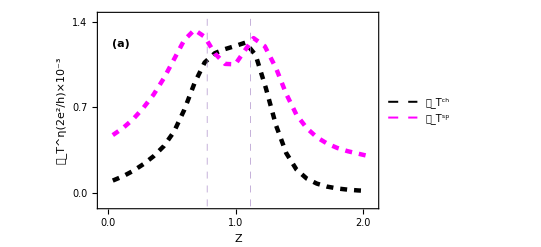

```mathematica
ListLinePlot[{DlTthcs[[All,{1,4}]],DlTths[[All,{1,4}]]},PlotRange->{-0.0001,0.00145},GridLines-> {{0.776,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tth^η(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tth^ch",16,Bold],Style["𝒟_Tth^sp",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

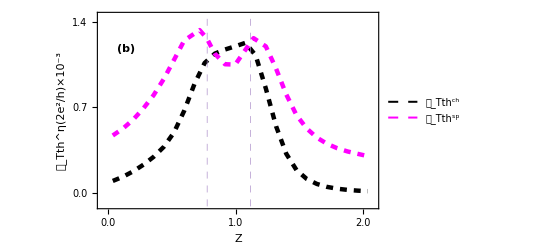

```mathematica
ListLinePlot[{DlTshcs[[All,{1,4}]],DlTshs[[All,{1,4}]]},PlotRange->{-0.0,0.00001},GridLines-> {{0.778,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^η(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],
FrameTicks->{{{{0.01,"1.0"},{0.00001,"0.01"},{0.0007,"0.7"},{0.000005,"0.005"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

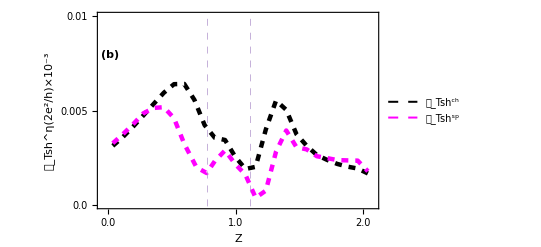

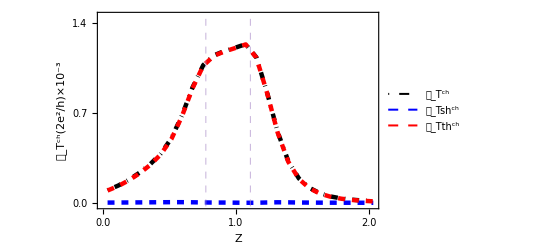

```mathematica
ListLinePlot[{DlTspcs[[All,{1,4}]],DlTshcs[[All,{1,4}]],DlTthcs[[All,{1,4}]]},PlotRange->{-0.000015,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^ch(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^ch",16,Bold],Style["𝒟_Tsh^ch",16,Bold],Style["𝒟_Tth^ch",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

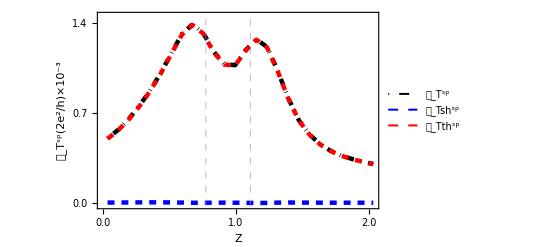

```mathematica
ListLinePlot[{DlTsps[[All,{1,4}]],DlTshs[[All,{1,4}]],DlTths[[All,{1,4}]]},PlotRange->{-0.000015,0.00145},GridLines-> {{0.776,1.11},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,DotDashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",22,Black,Bold,FontSlant->Italic],Style["𝒟_T^sp(2e^2/h)×10^-3",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"1.0"},{-0.0007,"-0.7"},{0.0007,"0.7"},{0.0014,"1.4"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,PlotLegends->Placed[{Style["𝒟_T^sp",16,Bold],Style["𝒟_Tsh^sp",16,Bold],Style["𝒟_Tth^sp",16,Bold]},{Right,Top}],ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large}]
```

```mathematica
DlTsps[[All,{1,5}]]
```

{{0.036,0.00567961948},{0.116,0.00584640955},{0.196,0.00582779115},{0.276,0.00558302715},{0.356,0.00505854339},{0.436,0.00443119658},{0.516,0.00401630383},{0.596,0.00407351188},{0.676,0.00410647046},{0.756,0.0037300369},{0.836,0.00346946215},{0.916,0.00375644844},{0.996,0.00259059989},{1.076,0.00214145845},{1.156,0.00195371677},{1.236,0.00295227159},{1.316,0.00371890716},{1.396,0.00320241606},{1.476,0.00259189099},{1.556,0.00302323474},{1.636,0.00325277272},{1.716,0.00366029024},{1.796,0.00406899841},{1.876,0.00454404521},{1.956,0.00494993262},{2.036,0.00411614541}}

```mathematica
DlTsps0={{0.516,0.00401630383090985000053277091376910582`9.532271139245948},{0.596,0.0040735118767233443496428369006377556`9.641389437203845},{0.676,0.00410647046369825786916756474083436528`9.698970004336019},{0.756,0.00373003689693283140648108582014381625`9.698970004336019},{0.836,0.00346946214919466080018167510179856346`9.698283285085353},{0.916,0.00375644843824101367613401934007575113`9.672946099630273},{0.9960000000000001,0.00259059989308202611393043483514782967`9.659934871299262},{1.076,0.00214145845210936010574490514636911281`9.684037199716988},{1.1560000000000001,0.00195371676521600146669050014203121539`9.698970004336019},{1.236,0.00295227158797143076937530486053677979`9.698970004336019},{1.316,0.00371890716368393863322812359037974334`9.589359407968585},{1.3960000000000001,0.00320241606311553943495161646913507416`9.40329260584428},{1.476,0.00259189099200337517388259189687007793`9.363888486592083}}
```

{{0.516,0.00401630383},{0.596,0.00407351188},{0.676,0.00410647046},{0.756,0.0037300369},{0.836,0.00346946215},{0.916,0.00375644844},{0.996,0.00259059989},{1.076,0.00214145845},{1.156,0.00195371677},{1.236,0.00295227159},{1.316,0.00371890716},{1.396,0.00320241606},{1.476,0.00259189099}}

```mathematica
DlTchcs[[All,{1,5}]]
```

{{0.036,0.0322521917},{0.116,0.0273865664},{0.196,0.0236084446},{0.276,0.0206117718},{0.356,0.0181490581},{0.436,0.0157673315},{0.516,0.0129139654},{0.596,0.00952161876},{0.676,0.00623617708},{0.756,0.00396932796},{0.836,0.00311382574},{0.916,0.00292535853},{0.996,0.00212402831},{1.076,0.00154616994},{1.156,0.00179008514},{1.236,0.00467241299},{1.316,0.0101112473},{1.396,0.0157177895},{1.476,0.0200629111},{1.556,0.0275356656},{1.636,0.0365159145},{1.716,0.0496042324},{1.796,0.065463921},{1.876,0.085787703},{1.956,0.11123415},{2.036,0.12916672}}

```mathematica
DlTchcs0={{0.516,0.01291396540796537375006297458591895628`9.489628576932967},{0.596,0.00952161876429976598014142754676452114`9.541617250863796},{0.676,0.00623617707988243028578852601128711823`9.601747841037344},{0.756,0.00396932796211893772883739552884454182`9.657494189005334},{0.836,0.00311382573745986387506613782670907673`9.698815838387324},{0.916,0.00292535852545327965597490397649263447`9.698970004336019},{0.9960000000000001,0.00212402831296623188040280972615070624`9.698970004336019},{1.076,0.00154616994188018149536361657317247732`9.698970004336019},{1.1560000000000001,0.00179008513737213184948381475824114005`9.677671642327027},{1.236,0.00467241298737571642529119136346456291`9.621719328982744},{1.316,0.01011124726876029135057520975501602804`9.547567315657188},{1.3960000000000001,0.0157177895266828970038027834964306585`9.458655853545123},{1.476,0.02006291106890325218228712562668027235`9.359169762043573}}
```

{{0.516,0.0129139654},{0.596,0.00952161876},{0.676,0.00623617708},{0.756,0.00396932796},{0.836,0.00311382574},{0.916,0.00292535853},{0.996,0.00212402831},{1.076,0.00154616994},{1.156,0.00179008514},{1.236,0.00467241299},{1.316,0.0101112473},{1.396,0.0157177895},{1.476,0.0200629111}}

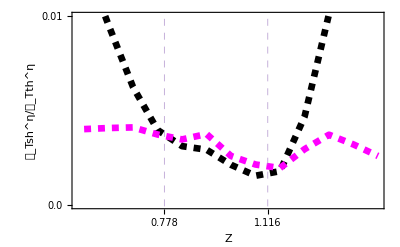

```mathematica
PDshth=ListLinePlot[{DlTchcs0[[All,{1,2}]],DlTsps0[[All,{1,2}]]},PlotRange->{-0.00,.01},GridLines-> {{0.778,1.116},None},GridLinesStyle->Directive[RGBColor[0.68417,0.56779,0.79798],Dashed],Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.012]},{Magenta,Dashed,Thickness[0.012]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,12,Bold],FrameLabel-> {Style["Z",12,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^η/𝒟_Tth^η",13,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.01,"0.01"},{0.05,"0.005"},{0.015,"0.015"},{0.0,"0.0"}},None},{{{0,"0.0"},{0.778,"0.778"},{1.116,"1.116"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{80,10},{60,30}},LabelStyle->{Bold,Large}]
```

```mathematica
ListLinePlot[{DlTchcs[[All,{1,5}]],DlTsps[[All,{1,5}]]},PlotRange->{-0.013,.2},Frame->True,FrameStyle->Thickness[0.005],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.008]}},FrameTicksStyle->Directive[Black,16,Bold],FrameLabel-> {Style["Z",20,Black,Bold,FontSlant->Italic],Style["𝒟_Tsh^η/𝒟_Tth^η",18,Black,Bold],Style["",19,Black,Bold]},LabelStyle->Directive[Bold,Large],
FrameTicks->{{{{0.1,"0.1"},{0.2,"0.2"},{2.14,"2.14"},{0.0,"0.0"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"}},None}},AxesStyle->Black,ImagePadding->{{88,10},{60,30}},LabelStyle->{Bold,Large},Epilog->{Inset[PDshth,Scaled[{.23,.44}],Scaled[{0,0}],1.8],PlotRange->{-0.2,0.003},PlotRangeClipping->False}]
```